```mathematica
SetOptions[Graphics,ImageSize->400];
```

```mathematica
fracTicks[n_]:=List[Sequence@@Table[{N[-2^(-i)],-2^(-i)},{i,0,n}],Sequence@@Table[{N[2^(-i)],2^(-i)},{i,0,n}]]
```

```mathematica
numDisk[{{x_,y_},{indxA_,indxB_},{occA_,occB_}}]:={Orange,Disk[{x,y},Scaled[{0.02, 0.02}]],Blue,Text[{occA,occB},{x,y}]}
numDisk[{{x_,y_},num_}]:={Orange,Disk[{x,y},Scaled[{0.02, 0.02}]],Blue,Text[num,{x,y}]}
```

```mathematica
Clear[plotRegionsFromList];
plotRegionsFromList[t_,color_:Blue,opacity_:0.6,text_:Null,yRange_:{0,2},opts:OptionsPattern[]]:=Module[{r,txt,txtPos},
txtPos=0.9 (yRange[[2]]-yRange[[1]])+ yRange[[1]];
If[TrueQ[text==Null],txt=Table[i,{i,1,Length[t]}],txt=text];
r=Table[{Opacity[opacity],color,Rectangle[{t[[i]],yRange[[1]]},{t[[i+1]],yRange[[2]]}],Opacity[1],Darker[color],Text[txt[[i]],{(t[[i+1]]+t[[i]])/2,txtPos}]},{i,1,Length[t]-1,2}];
Graphics[r,opts]]
```

```mathematica
Clear[MatrixFormCubeColor];
MatrixFormCubeColor[mat_,forgroundWhite_:1,backgroundWhite_:1]:=Module[{fg,bg },fg = forgroundWhite; bg={backgroundWhite,backgroundWhite-1};MatrixForm[{
MapThread[Style[#1,#2,Background->#3]&, {mat[[1]],Map[RGBColor,fg Transpose[RGBCube]],Map[RGBColor,bg[[1]]-bg[[2]] Transpose[RGBCube]]}],MapThread[Style[#1,#2,Background->#3]&, {mat[[2]],Map[RGBColor,fg Transpose[RGBCube]],Map[RGBColor,bg[[1]]-bg[[2]] Transpose[RGBCube]]}],MapThread[Style[#1,#2,Background->#3]&, {mat[[3]],Map[RGBColor,fg Transpose[RGBCube]],Map[RGBColor,bg[[1]]-bg[[2]] Transpose[RGBCube]]}]}]]
```

```mathematica
Clear[MatrixFormCubeColor];
MatrixFormCubeColor[mat_,backgroundWhite_:1]:=Module[{bg }, bg={backgroundWhite,backgroundWhite-1};MatrixForm[{
MapThread[Style[#1,Black,Background->#2]&, {mat[[1]],Map[RGBColor,bg[[1]]-bg[[2]] Transpose[RGBCube]]}],MapThread[Style[#1,Black,Background->#2]&, {mat[[2]],Map[RGBColor,bg[[1]]-bg[[2]] Transpose[RGBCube]]}],MapThread[Style[#1,Black,Background->#2]&, {mat[[3]],Map[RGBColor,bg[[1]]-bg[[2]] Transpose[RGBCube]]}]}]]
```

```mathematica
Clear[ApplyToPiecewise]
ApplyToPiecewise[func_,pwFunc_]:=Module[{},
posPi=Position[pwFunc,Piecewise];
If[Length[posPi]≥1,
pos =Table[Flatten[{Rest[posPi[[1]]],1,i,1}],{i,1,Length[pwFunc[[Sequence@@Rest[posPi[[1]]],1]]]}];
MapAt[func,pwFunc,pos],func[pwFunc]]]
```

```mathematica
Clear[simpleError]
simpleError[θ_,n_,R_:rR,round_:IntegerPart]:=Module[{nR,pos,out,rep,rules},
Unprotect[round];SetAttributes[round,Listable];Protect[round];
If[TrueQ[Head[R[θ]]==Piecewise],
pos =Position[R[θ],List[List[_,_,_],List[_,_,_],List[_,_,_]]];
nR=MapAt[round[2^n #]/(2^n)&,R[θ],pos]/.{round[2^n]-> 2^n,round[2^(n-1)]-> 2^(n-1)};
out=R[θ]; rep=Extract[R[θ],pos]-Extract[nR,pos];
rules=Table[pos[[i]]->rep[[i]],{i,1,Length[pos]}];
ReplacePart[out,rules],(round[2^n R[θ]]/(2^n)-R[θ]/.{round[2^n]-> 2^n,round[2^(n-1)]-> 2^(n-1)})]]
```

```mathematica
Clear[rRError,fRError,n];
rRError=Function[{θ,n,round},Evaluate[simpleError[θ,n,rR,round]]];
fRError=Function[{θ,n,round},Evaluate[simpleError[θ,n,fR,round]]];
```

```mathematica
Clear[rRErrorCube,fRErrorCube,n];
rRErrorCube=Function[{θ,n,round},Evaluate[rRError[θ,n,round].(2^n RGBCube)]];
fRErrorCube=Function[{θ,n,round},Evaluate[ApplyToPiecewise[#.(2^n RGBCube)&,fRError[θ,n,round]]]];
```

```mathematica
Clear[fRScaledError];
fRScaledError[θ_,m_,round_:IntegerPart]:=Piecewise[{
  {{{1, 1, 1}, 
{-(2^(1 - m)*Cos[θ]*round[2^(-1 + m)*Sec[θ]*Sin[Pi/6 + θ]]), Cos[θ], 
     -(2^(1 - m)*Cos[θ]*round[2^(-1 + m)*Sec[θ]*Sin[Pi/6 - θ]])},
 {-(2^(1 - m)*round[2^(-1 + m)*Cos[Pi/6 + θ]*Csc[θ]]*Sin[θ]), 
     -(Sin[θ]), 2^(1 - m)*round[2^(-1 + m)*Cos[Pi/6 - θ]*Csc[θ]]*Sin[θ]}}-rR[θ], 
   Inequality[Pi/6, LessEqual, Mod[θ, Pi/2], Less, Pi/3]}, 
  {{{1, 1, 1}, {-(2^(1 - m)*round[2^(-1 + m)*Csc[Pi/6 - θ]*Sin[Pi/6 + θ]]*Sin[Pi/6 - θ]), 
     2^(1 - m)*round[2^(-1 + m)*Cos[θ]*Csc[Pi/6 - θ]]*Sin[Pi/6 - θ], -(Sin[Pi/6 - θ])}, 
    {-(2^(1 - m)*Cos[Pi/6 - θ]*round[2^(-1 + m)*Cos[Pi/6 + θ]*Sec[Pi/6 - θ]]), 
     -(2^(1 - m)*Cos[Pi/6 - θ]*round[2^(-1 + m)*Sec[Pi/6 - θ]*Sin[θ]]), Cos[Pi/6 - θ]}}-rR[θ], 
   Inequality[Pi/3, LessEqual, Mod[θ, Pi/2], Less, Pi/2]},
{{{1, 1, 1}, {-(Sin[Pi/6 + θ]), 
   2^(1 - m)*round[2^(-1 + m)*Cos[θ]*Csc[Pi/6 + θ]]*Sin[Pi/6 + θ], 
   -(2^(1 - m)*round[2^(-1 + m)*Csc[Pi/6 + θ]*Sin[Pi/6 - θ]]*Sin[Pi/6 + θ])}, {-(Cos[Pi/6 + θ]), 
   -(2^(1 - m)*Cos[Pi/6 + θ]*round[2^(-1 + m)*Sec[Pi/6 + θ]*Sin[θ]]), 
   2^(1 - m)*Cos[Pi/6 + θ]*round[2^(-1 + m)*Cos[Pi/6 - θ]*Sec[Pi/6 + θ]]}}-rR[θ],Mod[θ, Pi/2] >= 0 || Mod[θ, Pi/2] < Pi/2}},Null]
```

```mathematica
Clear[fRScaledErrorCube,n];
fRScaledErrorCube=Function[{θ,n,round},Evaluate[ApplyToPiecewise[#.(2^n RGBCube)&,fRScaledError[θ,n,round]]]];
```

```mathematica
Clear[err,errR,rRfRErrorPlot];
```

```mathematica
rRfRErrorPlot[range_:{0,Pi/6},n_]:= Module[{},err[θ_]:=ApplyToPiecewise[#.RGBCube&,fRScaledError[θ,n,IntegerPart]];
errR[θ_]:=ApplyToPiecewise[#.RGBCube&,fRScaledError[θ,n,Round]];Grid[{{plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[2,i]]&,err[θ]],{i,1,8}],plot->Plot},plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[2,i]]&,errR[θ]],{i,1,8}],plot->Plot}},{plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[3,i]]&,err[θ]],{i,1,8}],plot->Plot},plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[3,i]]&,errR[θ]],{i,1,8}],plot->Plot}}}]]
```

```mathematica
Clear[simpleErrorPlot]
simpleErrorPlot[range_:{0,Pi/6},R_:rR,n_]:= Module[{},err[θ_]:=ApplyToPiecewise[#.RGBCube&,simpleError[θ,n,R,IntegerPart]];
errR[θ_]:=ApplyToPiecewise[#.RGBCube&,simpleError[θ,n,R,Round]];Grid[{{plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[2,i]]&,err[θ]],{i,1,8}],plot->Plot},plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[2,i]]&,errR[θ]],{i,1,8}],plot->Plot}},{plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[3,i]]&,err[θ]],{i,1,8}],plot->Plot},plot[f,{θ,range[[1]],range[[2]]},Ticks->{PiTicks[range[[1]],range[[2]],12],All},PlotStyle -> Map[RGBColor,Transpose[RGBCube]]]/. {f-> Table[ApplyToPiecewise[#[[3,i]]&,errR[θ]],{i,1,8}],plot->Plot}}}]]
```

```mathematica
plotError[n_,chan_,plotColors_:{Red,Green,Blue}, opts:OptionsPattern[]]:=Module[{pts,ptsB,pltFun},
pltFun[fun_,plotColor_,θ_, ops:OptionsPattern[]]:= Plot[fun,{θ,0,Pi},PlotRange->{All,{-2,2}},ExclusionsStyle-> None,Frame -> True,PlotStyle->plotColor,PlotLabel->Row[{StringJoin["The error in channel ",ToString[chan]," with R ∈ "],2^ToString[n]}],Evaluate[FilterRules[{ops}, Options[Plot]]]];
SetAttributes[pltFun,HoldFirst];
pts=Table[N[pointsIn[n,m,chan]],{m,0,6 2^( (n-1))}];
Show[{
pltFun[error[θ,θ][[chan,1]],plotColors[[1]],θ,opts],
pltFun[error[θ,θ][[chan,2]],plotColors[[2]],θ,opts],
pltFun[error[θ,θ][[chan,3]],plotColors[[3]],θ,opts],
pltFun[maxError[θ,θ][[chan,1]],Darker[plotColors[[1]]],θ,opts],
pltFun[maxError[θ,θ][[chan,2]],Darker[plotColors[[2]]],θ,opts],
pltFun[maxError[θ,θ][[chan,3]],Darker[plotColors[[3]]],θ,opts],ListPlot[pts[[All,3]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->{PointSize[0.03/2],Darker[plotColors[[3]]]}],
ListPlot[pts[[All,2]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->{PointSize[0.02/2],Darker[plotColors[[2]]]}],
ListPlot[pts[[All,1]],PlotRange->{All,{-2,2}},Frame -> True,PlotStyle->{PointSize[0.01/2],Darker[plotColors[[1]]]}]
}]
]
```

```mathematica
Clear[simpleErrorPlot,pltFun,err,errR]
simpleErrorPlot[range_:{0,Pi/2},errFun_:rRErrorCube,n_]:= Module[{},
Grid[{{
errorPlot[n,2,{range[[1]],range[[2]]},errFun, IntegerPart],
errorPlot[n,2,{range[[1]],range[[2]]},errFun, Round]},{
errorPlot[n,3,{range[[1]],range[[2]]},errFun, IntegerPart],
errorPlot[n,3,{range[[1]],range[[2]]},errFun, Round]}}]]
```

```mathematica
Clear[errorPlot,pltFun]
errorPlot[n_,chan_,range_:{0,Pi/2},errFun_:rRErrorCube, round_:IntegerPart,opts:OptionsPattern[]]:= Module[{},
pltFun[fun_,xRange_, ops:OptionsPattern[]]:= Plot[fun,xRange,
PlotRange->{range,All},
FrameTicks->{PiTicks[range[[1]],range[[2]],3(range[[2]]-range[[1]])/(Pi/6)],All},
ExclusionsStyle-> None,Frame -> True,
PlotStyle->Map[RGBColor,Transpose[RGBCube]],PlotLabel->StringJoin["The error in channel ",ToString[chan]," with R ∈ ",ToString[2^n]," using ",ToString[round]],ImageSize->400,Evaluate[FilterRules[{ops}, Options[Plot]]]];
plot[f,{θ,range[[1]],range[[2]]},opts]/. {f-> Table[ApplyToPiecewise[#[[chan,i]]&,errFun[θ,n,round]  ],{i,1,8}],plot->pltFun}
]
```

```mathematica
Clear[setupThetaRanges];
setupThetaRanges[n_]:=Module[{},
Clear[thetaOneVals,thetaOneMid,thetaOneRange,thetaOneToPoint,thetaTwoVals,thetaTwoMid,thetaTwoRange,thetaTwoToPoint,thetaVals,thetaMid,thetaRange,thetaToPoint];
thetaOneVals=thetaOne[n];
thetaOneMid=(Rest[thetaOneVals]+Most[thetaOneVals])/2;
thetaOneRange=Thread[Inequality[Most[thetaOneVals],Less,Mod[ θ,Pi/6],LessEqual,Rest[thetaOneVals]]];
thetaOneToPoint=Function[{θ},Evaluate[Piecewise[{{0,θ==0},Sequence@@Table[{i,thetaOneRange[[i]]},{i,1,Length[thetaOneRange]}]},Length[thetaOneRange]+1]]];
SetAttributes[thetaOneToPoint,Listable];
thetaTwoVals=thetaTwo[n];
thetaTwoMid=(Rest[thetaTwoVals]+Most[thetaTwoVals])/2;
thetaTwoRange=Thread[Inequality[Most[thetaTwoVals],Less,Mod[ θ,Pi/6],LessEqual,Rest[thetaTwoVals]]];
thetaTwoToPoint=Function[{θ},Evaluate[Piecewise[{{0,θ==0},Sequence@@Table[{i,thetaTwoRange[[i]]},{i,1,Length[thetaTwoRange]}]},Length[thetaOneRange]+1]]];
SetAttributes[thetaTwoToPoint,Listable];
thetaVals=Sort[Union[thetaOneVals,thetaTwoVals],Less];
thetaMid=(Rest[thetaVals]+Most[thetaVals])/2 ;
thetaRange = Thread[Inequality[Most[thetaVals],Less,Mod[ θ,Pi/6],LessEqual,Rest[thetaVals]]];
thetaToPoint=Function[{θ},{thetaOneToPoint[θ],thetaTwoToPoint[θ]}];
SetAttributes[thetaToPoint,Listable];
]
```

```mathematica
intersectionFromPoints[{p1_, p2_}, {p3_, p4_}] := 
  {(p1[[1]]*(p4[[1]]*(-p2[[2]] + p3[[2]]) + p3[[1]]*(p2[[2]] - p4[[2]])) + p2[[1]]*(p4[[1]]*(p1[[2]] - p3[[2]]) + p3[[1]]*(-p1[[2]] + p4[[2]])))/
    (p4[[1]]*(p1[[2]] - p2[[2]]) + p3[[1]]*(-p1[[2]] + p2[[2]]) + (p1[[1]] - p2[[1]])*(p3[[2]] - p4[[2]])), 
   (p4[[1]]*(p1[[2]] - p2[[2]])*p3[[2]] + p1[[1]]*p2[[2]]*p3[[2]] - p3[[1]]*p1[[2]]*p4[[2]] - p1[[1]]*p2[[2]]*p4[[2]] + p3[[1]]*p2[[2]]*p4[[2]] + 
     p2[[1]]*p1[[2]]*(-p3[[2]] + p4[[2]]))/(p4[[1]]*(p1[[2]] - p2[[2]]) + p3[[1]]*(-p1[[2]] + p2[[2]]) + (p1[[1]] - p2[[1]])*(p3[[2]] - p4[[2]]))}
```

```mathematica
eqnFromPoints[{x1_,y1_},{x2_,y2_}]:=Function[{x$},Evaluate[(x$ (-y1+y2))/(-x1+x2)+(-x2 y1+x1 y2)/(x1-x2)]];
```

```mathematica
Clear[errorMinTheta];
errorMinTheta[nn_]:=Module[{extraTheta,indx,order,pts1,pts2,thetaMidPoints,inter,occ,sum},
setupThetaRanges[nn]; 
pts1=ptsOne[nn];pts2=ptsTwo[nn];
thetaMidPoints=Map[thetaToPoint,thetaMid];
inter=Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}];
occ={Occurance[Transpose[thetaMidPoints][[1]],Reverse],Occurance[Transpose[thetaMidPoints][[2]]]};
sum=occ[[1]]+occ[[2]]-1;
inter=Transpose[{Sequence@@Transpose[inter],sum}];
extraTheta=Intersection[thetaOneVals,thetaTwoVals];
indx=Prepend[thetaMidPoints,sequence@@Map[thetaToPoint,extraTheta]]/.sequence->Sequence;
intersect=Prepend[inter,sequence@@Transpose[{extraTheta,Table[0,{i,1,Length[extraTheta]}],Table[0,{i,1,Length[extraTheta]}] }]]/.sequence->Sequence;
order=Ordering[N[intersect[[All,1]]]];
index=indx[[order]];
intersect[[order]]
]
```

```mathematica
Clear[errorMinTheta];
errorMinTheta[nn_]:=Module[{intersect,index,occurance,extraTheta,order,pts1,pts2,thetaMidPoints,inter,occ,pad},
setupThetaRanges[nn]; 
pts1=ptsOne[nn];pts2=ptsTwo[nn];
thetaMidPoints=Map[thetaToPoint,thetaMid];
inter=Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}];
occ=Transpose[{Occurance[Transpose[thetaMidPoints][[1]],Reverse],Occurance[Transpose[thetaMidPoints][[2]]]}];
extraTheta=Intersection[thetaOneVals,thetaTwoVals];
pad=Table[0,{i,1,Length[extraTheta]}];
index=Prepend[thetaMidPoints,sequence@@Map[thetaToPoint,extraTheta]]/.sequence->Sequence;
intersect=Prepend[inter,sequence@@Transpose[{extraTheta,pad }]]/.sequence->Sequence;
occurance=Prepend[occ,sequence@@Transpose[{pad,pad }]]/.sequence->Sequence;
order=Ordering[N[intersect[[All,1]]]];
index=index[[order]]; intersect=intersect[[order]]; occurance =occurance[[order]];
Transpose[{intersect,index,occurance}]
]
```

```mathematica
classifyByNegPowerOfTwo[{{x_,y_},{indxA_,indxB_},{occA_,occB_}}]:={{x,y},Ceiling[-Log[Abs[y]]/Log[2]]}
```

```mathematica
classifyByPosition[{{x_,y_},{indxA_,indxB_},{occA_,occB_}}]:={{x,y},occA+occB+1}
```

```mathematica
Clear[convRound];convRound[{{x_,y_},{indxA_,indxB_},{occA_,occB_}}]:={{x,If[y< 0.5,y,y-1]},{indxA,indxB},{occA,occB}}
```

```mathematica
Occurance[idx_,fun_:Flatten]:=Module[{min,max,occurCount,occur,pos,cnt},
min=Min[idx];
max=Max[idx];
occurCount=Table[i,{i,min,max}];
occur=Table[0,{i,1,Length[idx]}];
For[i=min,i≤max,i++,
pos=Flatten[Position[idx,i]];
cnt=Table[i,{i,1,Length[pos]}];
occur[[pos]]=fun[cnt];];
occur]
```

```mathematica
MatrixFormCubeColor[RGBCube,0.7]
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

# Representations of the Rotation

There are two matrices we are interested in approximating.
The reduced Rotation

```mathematica
Row[{"rR[θ] = ",MatrixForm[rR[θ]]}]
```

rR[θ] = (1 | 1 | 1
-Sin[π/6+θ] | Cos[θ] | -Sin[π/6-θ]
-Cos[π/6+θ] | -Sin[θ] | Cos[π/6-θ])

and the factored Rotation

```mathematica
mat = fR[θ,2];
factor=fRScale[θ,1];
Row[{"rR[θ] = fRScale[θ] fR[θ] = ",TableForm[Table[{MatrixForm[factor[[1,i,1]]]⊗  MatrixForm[mat[[1,i,1]]],mat[[1,i,2]]},{i,1,3}]]}]
```

rR[θ] = (1
-2 Sin[π/6+θ]
-2 Cos[π/6+θ])⊗(1 | 1 | 1
1 | -Cos[θ] Csc[π/6+θ] | Csc[π/6+θ] Sin[π/6-θ]
1 | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ]) | 0≤Mod[θ,π/2]<π/6
(1
2 Cos[θ]
-2 Sin[θ])⊗(1 | 1 | 1
-Sec[θ] Sin[π/6+θ] | 1 | -Sec[θ] Sin[π/6-θ]
Cos[π/6+θ] Csc[θ] | 1 | -Cos[π/6-θ] Csc[θ]) | π/6≤Mod[θ,π/2]<π/3
(1
-2 Sin[π/6-θ]
2 Cos[π/6-θ])⊗(1 | 1 | 1
Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1
-Cos[π/6+θ] Sec[π/6-θ] | -Sec[π/6-θ] Sin[θ] | 1) | π/3≤Mod[θ,π/2]<π/2

## Approximating rR

```mathematica
Row[{"rRError[θ] = rR[θ]- Approx[rR[θ]] = ",MatrixForm[rRError[θ,n,Round]]}]
```

rRError[θ] = rR[θ]- Approx[rR[θ]] = (0 | 0 | 0
-2^-n Round[2^n Sin[π/6+θ]]+Sin[π/6+θ] | -Cos[θ]+2^-n Round[2^n Cos[θ]] | -2^-n Round[2^n Sin[π/6-θ]]+Sin[π/6-θ]
Cos[π/6+θ]-2^-n Round[2^n Cos[π/6+θ]] | -2^-n Round[2^n Sin[θ]]+Sin[θ] | -Cos[π/6-θ]+2^-n Round[2^n Cos[π/6-θ]])

```mathematica
Row[{"rRErrorCube[θ] = rRError[θ].RGBCube = ",MatrixFormCubeColor[rRErrorCube[θ,n,Round],0.7]}]
```

rRErrorCube[θ] = rRError[θ].RGBCube = (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/8 Round[8 Sin[π/6+θ]]+Sin[π/6+θ] | -Cos[θ]+1/8 Round[8 Cos[θ]]-1/8 Round[8 Sin[π/6+θ]]+Sin[π/6+θ] | -Cos[θ]+1/8 Round[8 Cos[θ]] | -Cos[θ]+1/8 Round[8 Cos[θ]]-1/8 Round[8 Sin[π/6-θ]]+Sin[π/6-θ] | -1/8 Round[8 Sin[π/6-θ]]+Sin[π/6-θ] | -1/8 Round[8 Sin[π/6-θ]]-1/8 Round[8 Sin[π/6+θ]]+Sin[π/6-θ]+Sin[π/6+θ] | -Cos[θ]+1/8 Round[8 Cos[θ]]-1/8 Round[8 Sin[π/6-θ]]-1/8 Round[8 Sin[π/6+θ]]+Sin[π/6-θ]+Sin[π/6+θ]
0 | Cos[π/6+θ]-1/8 Round[8 Cos[π/6+θ]] | Cos[π/6+θ]-1/8 Round[8 Cos[π/6+θ]]-1/8 Round[8 Sin[θ]]+Sin[θ] | -1/8 Round[8 Sin[θ]]+Sin[θ] | -Cos[π/6-θ]+1/8 Round[8 Cos[π/6-θ]]-1/8 Round[8 Sin[θ]]+Sin[θ] | -Cos[π/6-θ]+1/8 Round[8 Cos[π/6-θ]] | -Cos[π/6-θ]+Cos[π/6+θ]+1/8 Round[8 Cos[π/6-θ]]-1/8 Round[8 Cos[π/6+θ]] | -Cos[π/6-θ]+Cos[π/6+θ]+1/8 Round[8 Cos[π/6-θ]]-1/8 Round[8 Cos[π/6+θ]]-1/8 Round[8 Sin[θ]]+Sin[θ])

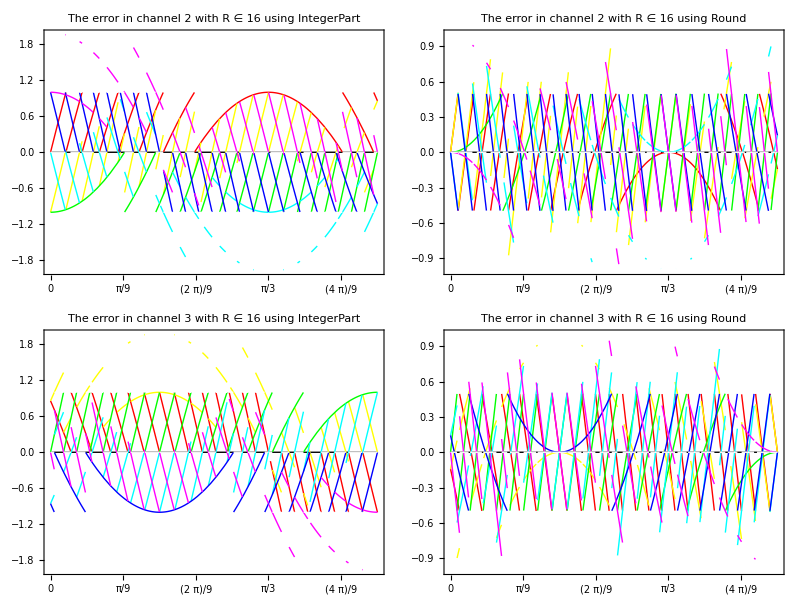

```mathematica
simpleErrorPlot[{0,Pi/2},rRErrorCube,4]
```

## Approximating fR

```mathematica
Row[{"fRError[θ] = fR[θ]- Approx[fR[θ]] = ",ApplyToPiecewise[ MatrixForm,fRError[θ,n,Round]]}]
```

fRError[θ] = fR[θ]- Approx[fR[θ]] = Piecewise[{{(0 | 0 | 0
0 | -1/2 Cos[θ] Csc[π/6+θ]+2^-n Round[2^(-1+n) Cos[θ] Csc[π/6+θ]] | -2^-n Round[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]+1/2 Csc[π/6+θ] Sin[π/6-θ]
0 | -2^-n Round[2^(-1+n) Sec[π/6+θ] Sin[θ]]+1/2 Sec[π/6+θ] Sin[θ] | 2^-n Round[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 Cos[π/6-θ] Sec[π/6+θ]), 0≤Mod[θ,π/2]<π/6}, {(0 | 0 | 0
2^-n Round[2^(-1+n) Sec[θ] Sin[π/6+θ]]-1/2 Sec[θ] Sin[π/6+θ] | 0 | 2^-n Round[2^(-1+n) Sec[θ] Sin[π/6-θ]]-1/2 Sec[θ] Sin[π/6-θ]
1/2 Cos[π/6+θ] Csc[θ]-2^-n Round[2^(-1+n) Cos[π/6+θ] Csc[θ]] | 0 | -1/2 Cos[π/6-θ] Csc[θ]+2^-n Round[2^(-1+n) Cos[π/6-θ] Csc[θ]]), π/6≤Mod[θ,π/2]<π/3}, {(0 | 0 | 0
-2^-n Round[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]]+1/2 Csc[π/6-θ] Sin[π/6+θ] | -1/2 Cos[θ] Csc[π/6-θ]+2^-n Round[2^(-1+n) Cos[θ] Csc[π/6-θ]] | 0
2^-n Round[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]-1/2 Cos[π/6+θ] Sec[π/6-θ] | 2^-n Round[2^(-1+n) Sec[π/6-θ] Sin[θ]]-1/2 Sec[π/6-θ] Sin[θ] | 0), π/3≤Mod[θ,π/2]<π/2}, {Null, True}}]

```mathematica
ApplyToPiecewise[MatrixFormCubeColor[#,0.7]&,fRErrorCube[θ,n,int]]
```

Piecewise[{{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2^n (-1/2 Cos[θ] Csc[π/6+θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6+θ]]) | 2^n (-1/2 Cos[θ] Csc[π/6+θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6+θ]]) | 2^n (-1/2 Cos[θ] Csc[π/6+θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6+θ]])+2^n (-2^-n int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]+1/2 Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-2^-n int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]+1/2 Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-2^-n int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]+1/2 Csc[π/6+θ] Sin[π/6-θ]) | 2^n (-1/2 Cos[θ] Csc[π/6+θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6+θ]])+2^n (-2^-n int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]+1/2 Csc[π/6+θ] Sin[π/6-θ])
0 | 0 | 2^n (-2^-n int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+1/2 Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+1/2 Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[-2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 Cos[π/6-θ] Sec[π/6+θ])+2^n (-2^-n int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+1/2 Sec[π/6+θ] Sin[θ]) | 2^n (-2^-n int[-2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 Cos[π/6-θ] Sec[π/6+θ]) | 2^n (-2^-n int[-2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 Cos[π/6-θ] Sec[π/6+θ]) | 2^n (-2^-n int[-2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]-1/2 Cos[π/6-θ] Sec[π/6+θ])+2^n (-2^-n int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+1/2 Sec[π/6+θ] Sin[θ])), 0≤Mod[θ,π/2]<π/6}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6+θ]]-1/2 Sec[θ] Sin[π/6+θ]) | 2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6+θ]]-1/2 Sec[θ] Sin[π/6+θ]) | 0 | 2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6-θ]]-1/2 Sec[θ] Sin[π/6-θ]) | 2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6-θ]]-1/2 Sec[θ] Sin[π/6-θ]) | 2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6-θ]]-1/2 Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6+θ]]-1/2 Sec[θ] Sin[π/6+θ]) | 2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6-θ]]-1/2 Sec[θ] Sin[π/6-θ])+2^n (-2^-n int[-2^(-1+n) Sec[θ] Sin[π/6+θ]]-1/2 Sec[θ] Sin[π/6+θ])
0 | 2^n (1/2 Cos[π/6+θ] Csc[θ]-2^-n int[2^(-1+n) Cos[π/6+θ] Csc[θ]]) | 2^n (1/2 Cos[π/6+θ] Csc[θ]-2^-n int[2^(-1+n) Cos[π/6+θ] Csc[θ]]) | 0 | 2^n (-1/2 Cos[π/6-θ] Csc[θ]-2^-n int[-2^(-1+n) Cos[π/6-θ] Csc[θ]]) | 2^n (-1/2 Cos[π/6-θ] Csc[θ]-2^-n int[-2^(-1+n) Cos[π/6-θ] Csc[θ]]) | 2^n (-1/2 Cos[π/6-θ] Csc[θ]-2^-n int[-2^(-1+n) Cos[π/6-θ] Csc[θ]])+2^n (1/2 Cos[π/6+θ] Csc[θ]-2^-n int[2^(-1+n) Cos[π/6+θ] Csc[θ]]) | 2^n (-1/2 Cos[π/6-θ] Csc[θ]-2^-n int[-2^(-1+n) Cos[π/6-θ] Csc[θ]])+2^n (1/2 Cos[π/6+θ] Csc[θ]-2^-n int[2^(-1+n) Cos[π/6+θ] Csc[θ]])), π/6≤Mod[θ,π/2]<π/3}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^-n int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]]+1/2 Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-1/2 Cos[θ] Csc[π/6-θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6-θ]])+2^n (-2^-n int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]]+1/2 Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-1/2 Cos[θ] Csc[π/6-θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6-θ]]) | 2^n (-1/2 Cos[θ] Csc[π/6-θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6-θ]]) | 0 | 2^n (-2^-n int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]]+1/2 Csc[π/6-θ] Sin[π/6+θ]) | 2^n (-1/2 Cos[θ] Csc[π/6-θ]-2^-n int[-2^(-1+n) Cos[θ] Csc[π/6-θ]])+2^n (-2^-n int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]]+1/2 Csc[π/6-θ] Sin[π/6+θ])
0 | 2^n (-2^-n int[-2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]-1/2 Cos[π/6+θ] Sec[π/6-θ]) | 2^n (-2^-n int[-2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]-1/2 Cos[π/6+θ] Sec[π/6-θ])+2^n (-2^-n int[-2^(-1+n) Sec[π/6-θ] Sin[θ]]-1/2 Sec[π/6-θ] Sin[θ]) | 2^n (-2^-n int[-2^(-1+n) Sec[π/6-θ] Sin[θ]]-1/2 Sec[π/6-θ] Sin[θ]) | 2^n (-2^-n int[-2^(-1+n) Sec[π/6-θ] Sin[θ]]-1/2 Sec[π/6-θ] Sin[θ]) | 0 | 2^n (-2^-n int[-2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]-1/2 Cos[π/6+θ] Sec[π/6-θ]) | 2^n (-2^-n int[-2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]-1/2 Cos[π/6+θ] Sec[π/6-θ])+2^n (-2^-n int[-2^(-1+n) Sec[π/6-θ] Sin[θ]]-1/2 Sec[π/6-θ] Sin[θ])), π/3≤Mod[θ,π/2]<π/2}, {Null, True}}]

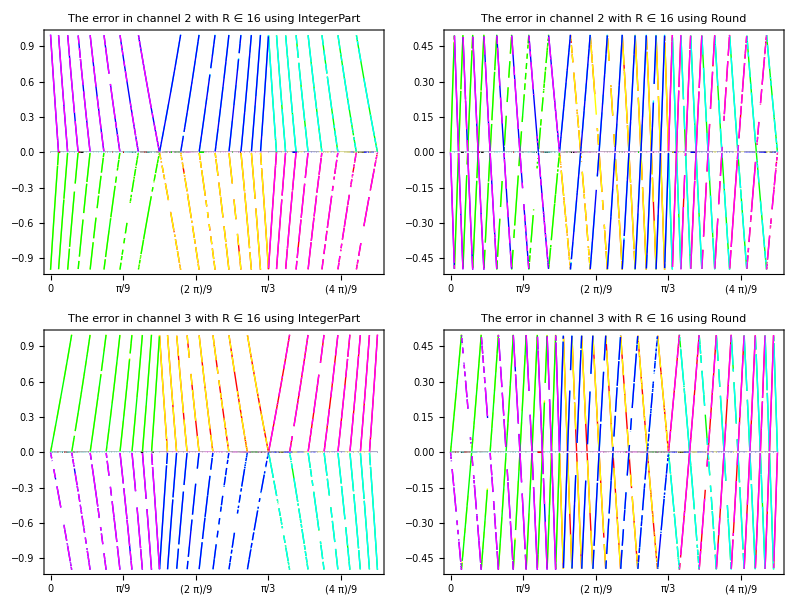

```mathematica
simpleErrorPlot[{0,Pi/2},fRErrorCube,4]
```

The base function for the channel error

```mathematica
2^n (-2^-n int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]]+1/2 Csc[π/6+θ] Sin[π/6-θ])  2^n (-2^-n int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+1/2 Sec[π/6+θ] Sin[θ])
```

```mathematica
Clear[errOne,errTwo];
```

```mathematica
errTwo[θ_,n_,int_]:=2^n((-2^(-n))*int[2^(-1 + n)*Sec[Pi/6 + θ]*Sin[θ]] + (1/2)*Sec[Pi/6 + θ]*Sin[θ])
```

```mathematica
errOne[θ_,n_,int_]:=2^n((-2^(-n))*int[2^(-1 + n)*Csc[Pi/6 + θ]*Sin[Pi/6 - θ]] + (1/2)*Csc[Pi/6 + θ]*Sin[Pi/6 - θ]);
```

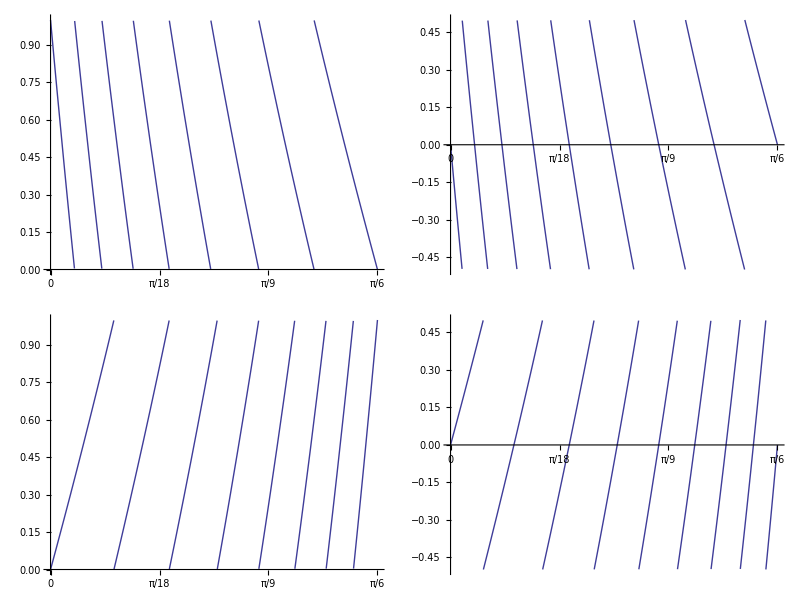

```mathematica
Grid[{{Plot[errOne[θ,4,IntegerPart],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],Plot[errOne[θ,4,Round],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}]},
{Plot[errTwo[θ,4,IntegerPart],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],Plot[errTwo[θ,4,Round],{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}]}}]
```

to find the zeros we need to solve

sin(π/6-θ)==2^(1-n) sin(θ+π/6) int(2^(n-1) sin(π/6-θ) csc(θ+π/6))

```mathematica
2^(n-1) sin(π/6-θ) csc(θ+π/6)== int(2^(n-1) sin(π/6-θ) csc(θ+π/6))
```

```mathematica
Simplify[Assuming[Element[θ,Reals]&& θ≥ 0 && θ≤ Pi/6, Solve[y== Csc[π/6+θ] Sin[π/6 - θ],θ]]]
```

{{θ→ConditionalExpression[ArcTan[-(√3 (1+y))/(√(1+y+y^2)),(-1+y)/(√(1+y+y^2))]+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))]+2 π C[1],C[1]∈Integers]}}

For a given value of n there are 2^(n - 1) + 1 zeros between 0 and Pi/6

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n-1))],{i,2^(n-1),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n-1))],{i,0,2^(n-1)}]]
```

```mathematica
nn=4;
setupThetaRanges[nn];
```

The min and max points are then found by using the values for theta

```mathematica
Clear[ptsOne,ptsTwo]
ptsOne[n_]:=Module[{thetaPts},thetaPts=thetaOne[n];{Transpose[{Most[thetaPts],Table[1,{i,1,2^(n-1)}]}],Transpose[{Rest[thetaPts],Table[0,{i,1,2^(n-1)}]}]}]
ptsTwo[n_]:=Module[{thetaPts},thetaPts=thetaTwo[n];{Transpose[{Most[thetaPts],Table[0,{i,1,2^(n-1)}]}],Transpose[{Rest[thetaPts],Table[1,{i,1,2^(n-1)}]}]}]
```

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOne[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsOne[nn];Show[{Plot[{errOne[θ,nn,IntegerPart]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
plotErrorWithLinesAndPointsTwo[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsTwo[nn];Show[{Plot[{errTwo[θ,nn,IntegerPart]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
```

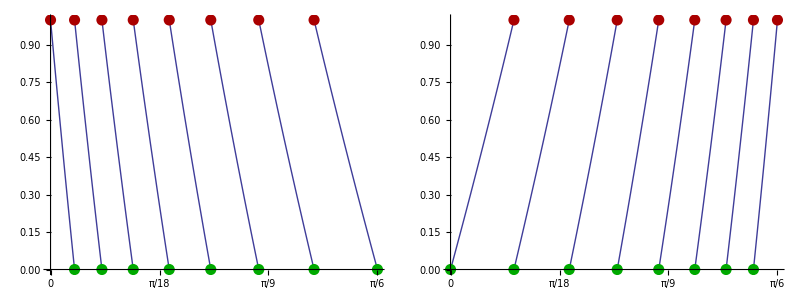

```mathematica
Grid[{{plotErrorWithLinesAndPointsOne[4],plotErrorWithLinesAndPointsTwo[4]}}]
```

We now need to find the intersecting points between the channels.
  To do this we first need to divide up the range into regions where there is only one intersection.

```mathematica
nn=4;
setupThetaRanges[nn];
```

```mathematica
TableForm[{thetaOneVals,thetaTwoVals}]
```

0 | ArcTan[1/(15 √3)] | ArcTan[1/(7 √3)] | ArcTan[(√3)/13] | ArcTan[1/(3 √3)] | ArcTan[5/(11 √3)] | ArcTan[(√3)/5] | ArcTan[7/(9 √3)] | π/6
0 | ArcTan[(√3)/17] | ArcTan[1/(3 √3)] | ArcTan[(3 √3)/19] | ArcTan[(√3)/5] | ArcTan[5/(7 √3)] | ArcTan[(3 √3)/11] | ArcTan[(7 √3)/23] | π/6

in each range we want to find the point of intersection between the errors for this we need to know which of the individual regions we are in for each of the channels.

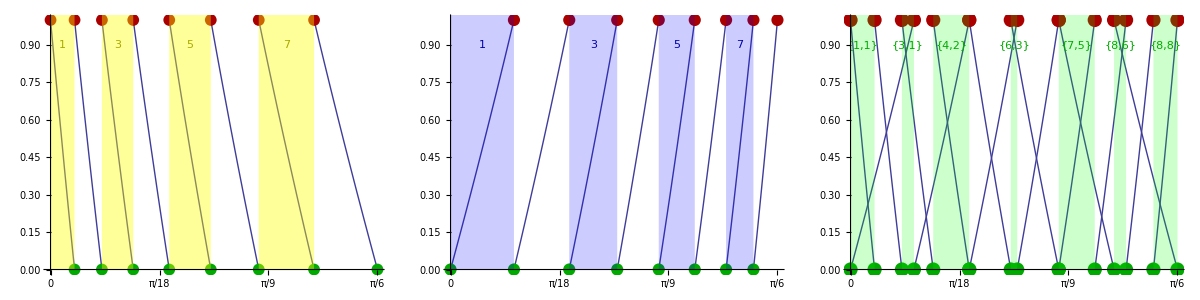

```mathematica
Grid[{{Show[{plotErrorWithLinesAndPointsOne[nn],plotRegionsFromList[thetaOne[nn],Yellow,0.4]}],Show[{plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaTwo[nn],Blue,0.2]}],Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]]}]
}}]
```

in each of the green intersecting regions we need the equatiuon of the lines to find the point of intersection. We use a linear approximation to find the points of intersection.

```mathematica
thetaMidPoints =Map[thetaToPoint,thetaMid];
pts1=ptsOne[nn];
pts2=ptsTwo[nn];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]]
```

{{0.0278999,0.274781},{0.0574832,0.566142},{0.0886554,0.873151},{0.121276,0.222839},{0.155194,0.6057},{0.225777,0.46404},{0.261799,0.932906},{0.297822,0.46404},{0.368404,0.6057},{0.402322,0.222839},{0.434943,0.873151},{0.466116,0.566142},{0.495699,0.274781}}

```mathematica
plotErrorIntersect[nn_,color_:Red,size_:0.02]:=Module[{minMaxPts},
thetaRanges[nn]; pts1=ptsOne[nn];
pts2=ptsTwo[nn];thetaMidPoints=Map[thetaToPoint,thetaMid];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]];
ListPlot[intersect,PlotStyle->{PointSize[size],Darker[color]}]]
```

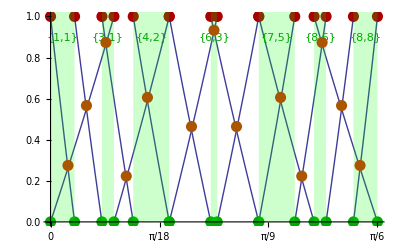

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],plotErrorIntersect[nn,Orange]}]
```

One missed point is where both happen to be zero!

```mathematica
intersect=errorMinTheta[4];
TableForm[{intersect[[All,1]],intersect[[All,2]]}]
```

0
0 | (ArcTan[1/(15 √3)] ArcTan[(√3)/17])/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17])
ArcTan[1/(15 √3)]/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17]) | (ArcTan[1/(7 √3)] ArcTan[(√3)/17])/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17])
ArcTan[1/(7 √3)]/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17]) | (ArcTan[(√3)/17] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13])
ArcTan[(√3)/13]/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13]) | (-ArcTan[1/(7 √3)] ArcTan[(√3)/17]+ArcTan[1/(3 √3)] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13])
(-ArcTan[(√3)/17]+ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13]) | (ArcTan[1/(3 √3)]^2-ArcTan[(√3)/17] ArcTan[(√3)/13])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13])
(ArcTan[1/(3 √3)]-ArcTan[(√3)/17])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13]) | ArcTan[1/(3 √3)]
0 | (-ArcTan[1/(3 √3)]^2+ArcTan[5/(11 √3)] ArcTan[(3 √3)/19])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19])
(-ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]) | (-ArcTan[1/(3 √3)] ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19] ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5])
(-ArcTan[1/(3 √3)]+ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5]) | (-ArcTan[5/(11 √3)] ArcTan[(3 √3)/19]+ArcTan[(√3)/5]^2)/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5])
(-ArcTan[(3 √3)/19]+ArcTan[(√3)/5])/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5]) | ArcTan[(√3)/5]
0 | (ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]-ArcTan[(√3)/5]^2)/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5])
(ArcTan[7/(9 √3)]-ArcTan[(√3)/5])/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5]) | (-ArcTan[5/(7 √3)] ArcTan[(√3)/5]+ArcTan[7/(9 √3)] ArcTan[(3 √3)/11])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11])
(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11]) | (-ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]+1/6 π ArcTan[(3 √3)/11])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11])
(π/6-ArcTan[5/(7 √3)])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11]) | (-ArcTan[7/(9 √3)] ArcTan[(3 √3)/11]+1/6 π ArcTan[(7 √3)/23])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23])
(π/6-ArcTan[(3 √3)/11])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23]) | (π^2/36-ArcTan[7/(9 √3)] ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23])
(π/6-ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23]) | π/6
0
0
0 | 1
1 | 2
1 | 3
1 | 3
2 | 4
2 | 4
2 | 5
3 | 6
3 | 6
4 | 6
4 | 7
5 | 7
6 | 8
6 | 8
7 | 8
8 | 9
9

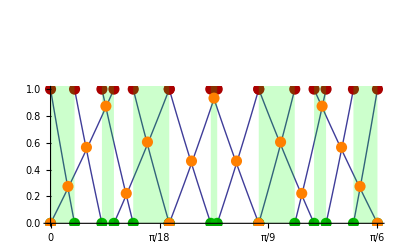

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],ListPlot[intersect[[All,1]],PlotStyle->{PointSize[0.02],Orange}]}]
```

The relationship to the round error

The intersecting points where the combined error is minimised are at the same points as for the truncated function in the theta direction.

```mathematica
intersectRound=Map[convRound,intersect];
intersectRoundPos=Map[classifyByPosition,intersectRound];
```

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOneR[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsOne[nn];Show[{Plot[{errOne[θ,nn,Round]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
plotErrorWithLinesAndPointsTwoR[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsTwo[nn];Show[{Plot[{errTwo[θ,nn,Round]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
```

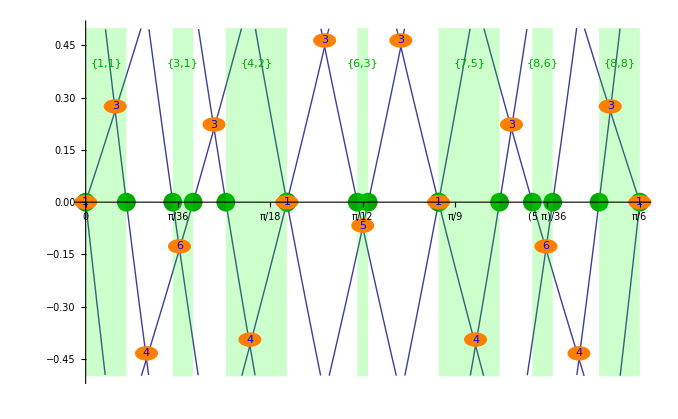

```mathematica
Show[{plotErrorWithLinesAndPointsOneR[nn],plotErrorWithLinesAndPointsTwoR[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid],{-0.5,0.5}],Graphics[Map[numDisk,intersectRoundPos]]},PlotRange->{{0,Pi/6},{-0.5,0.5}}]
```

Next we need to classify the points by the size of the error

One way to classify is by the order of the points on the lines.

```mathematica
intersectPos=Map[classifyByPosition,intersect];
```

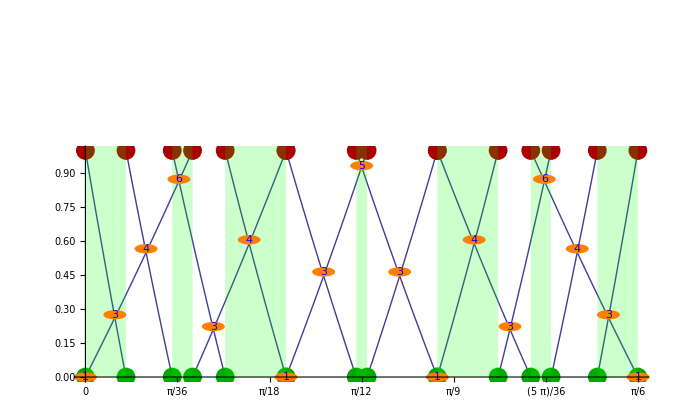

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],Graphics[Map[numDisk,intersectPos]]}]
```

Another is by the size of the error relative to negative powers of two ie 1, 0.5, 0.25, ...

```mathematica
classifyByNegPowerOfTwo[{x_,y_,class_}]:={x,y,Ceiling[-Log[Abs[y]]/Log[2]]}
```

```mathematica
intersectClassified=Map[classifyByNegPowerOfTwo,intersect]
```

{{0,0,∞},{(ArcTan[1/(15 √3)] ArcTan[(√3)/17])/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17]),ArcTan[1/(15 √3)]/(ArcTan[1/(15 √3)]+ArcTan[(√3)/17]),2},{(ArcTan[1/(7 √3)] ArcTan[(√3)/17])/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17]),ArcTan[1/(7 √3)]/(-ArcTan[1/(15 √3)]+ArcTan[1/(7 √3)]+ArcTan[(√3)/17]),1},{(ArcTan[(√3)/17] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13]),ArcTan[(√3)/13]/(-ArcTan[1/(7 √3)]+ArcTan[(√3)/17]+ArcTan[(√3)/13]),1},{(-ArcTan[1/(7 √3)] ArcTan[(√3)/17]+ArcTan[1/(3 √3)] ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13]),(-ArcTan[(√3)/17]+ArcTan[(√3)/13])/(-ArcTan[1/(7 √3)]+ArcTan[1/(3 √3)]-ArcTan[(√3)/17]+ArcTan[(√3)/13]),3},{(ArcTan[1/(3 √3)]^2-ArcTan[(√3)/17] ArcTan[(√3)/13])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13]),(ArcTan[1/(3 √3)]-ArcTan[(√3)/17])/(2 ArcTan[1/(3 √3)]-ArcTan[(√3)/17]-ArcTan[(√3)/13]),1},{ArcTan[1/(3 √3)],0,∞},{(-ArcTan[1/(3 √3)]^2+ArcTan[5/(11 √3)] ArcTan[(3 √3)/19])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]),(-ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)])/(-2 ArcTan[1/(3 √3)]+ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]),2},{(-ArcTan[1/(3 √3)] ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19] ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5]),(-ArcTan[1/(3 √3)]+ArcTan[(√3)/5])/(-ArcTan[1/(3 √3)]-ArcTan[5/(11 √3)]+ArcTan[(3 √3)/19]+ArcTan[(√3)/5]),1},{(-ArcTan[5/(11 √3)] ArcTan[(3 √3)/19]+ArcTan[(√3)/5]^2)/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5]),(-ArcTan[(3 √3)/19]+ArcTan[(√3)/5])/(-ArcTan[5/(11 √3)]-ArcTan[(3 √3)/19]+2 ArcTan[(√3)/5]),2},{ArcTan[(√3)/5],0,∞},{(ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]-ArcTan[(√3)/5]^2)/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5]),(ArcTan[7/(9 √3)]-ArcTan[(√3)/5])/(ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-2 ArcTan[(√3)/5]),1},{(-ArcTan[5/(7 √3)] ArcTan[(√3)/5]+ArcTan[7/(9 √3)] ArcTan[(3 √3)/11])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11]),(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)])/(-ArcTan[5/(7 √3)]+ArcTan[7/(9 √3)]-ArcTan[(√3)/5]+ArcTan[(3 √3)/11]),3},{(-ArcTan[5/(7 √3)] ArcTan[7/(9 √3)]+1/6 π ArcTan[(3 √3)/11])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11]),(π/6-ArcTan[5/(7 √3)])/(π/6-ArcTan[5/(7 √3)]-ArcTan[7/(9 √3)]+ArcTan[(3 √3)/11]),1},{(-ArcTan[7/(9 √3)] ArcTan[(3 √3)/11]+1/6 π ArcTan[(7 √3)/23])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23]),(π/6-ArcTan[(3 √3)/11])/(π/6-ArcTan[7/(9 √3)]-ArcTan[(3 √3)/11]+ArcTan[(7 √3)/23]),1},{(π^2/36-ArcTan[7/(9 √3)] ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23]),(π/6-ArcTan[(7 √3)/23])/(π/3-ArcTan[7/(9 √3)]-ArcTan[(7 √3)/23]),2},{π/6,0,∞}}

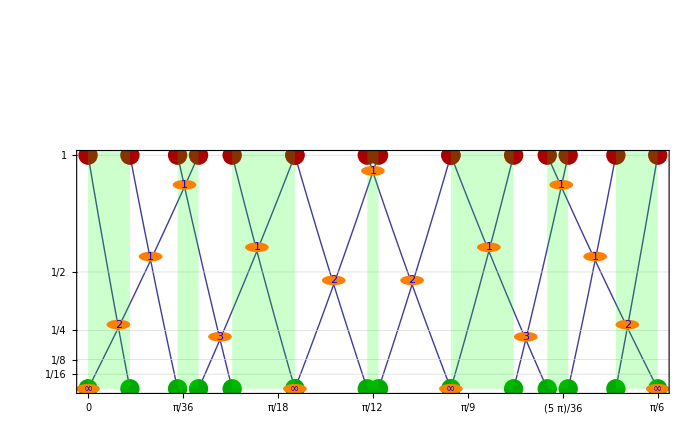

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],Graphics[Map[numDisk,intersectClassified]]},Frame->True,GridLines->{None,Table[N[2^(-i)],{i,0,4}]},FrameTicks->{PiTicks[0,Pi/6,6],Table[{N[2^(-i)],2^(-i)},{i,0,4}]}]
```

```mathematica
intersectRoundClassified=Map[classifyByNegPowerOfTwo,intersectRound];
```

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],Graphics[Map[numDisk,intersectRoundClassified]]},Frame->True,GridLines->{None,Table[N[2^(-i)],{i,0,4}]},FrameTicks->{PiTicks[0,Pi/6,6],Table[{N[2^(-i)],2^(-i)},{i,0,4}]}]
```

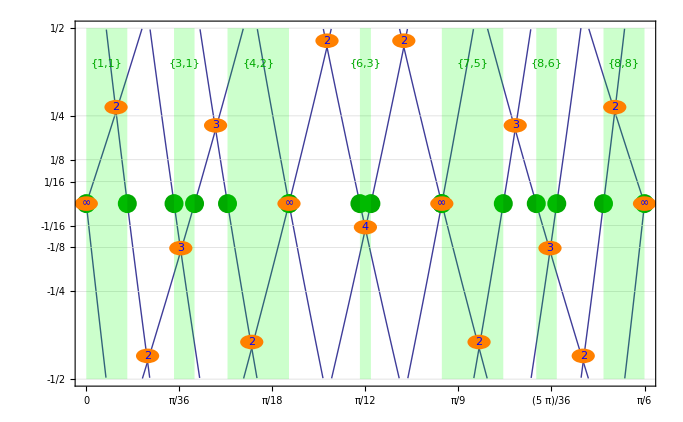

```mathematica
Show[{plotErrorWithLinesAndPointsOneR[nn],plotErrorWithLinesAndPointsTwoR[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid],{-0.5,0.5}],Graphics[Map[numDisk,intersectRoundClassified]]},PlotRange->{{0,Pi/6},{-0.5,0.5}},Frame->True,GridLines->{None,fracTicks[nn][[All,1]]},FrameTicks->{PiTicks[0,Pi/6,6],fracTicks[nn]}]
```

## Approximating rR with fR

```mathematica
ApplyToPiecewise[MatrixFormCubeColor[#,0.7]&,fRScaledErrorCube[θ,n,int]]
```

Piecewise[{{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ]) | 0 | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ])+2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ]) | 2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6-θ]]+Sin[π/6-θ])+2^n (-2^(1-n) Cos[θ] int[2^(-1+n) Sec[θ] Sin[π/6+θ]]+Sin[π/6+θ])
0 | 2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ]) | 2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ]) | 0 | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ])+2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) int[2^(-1+n) Cos[π/6-θ] Csc[θ]] Sin[θ])+2^n (Cos[π/6+θ]-2^(1-n) int[2^(-1+n) Cos[π/6+θ] Csc[θ]] Sin[θ])), π/6≤Mod[θ,π/2]<π/3}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ])+2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ]) | 0 | 2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6-θ]] Sin[π/6-θ])+2^n (-2^(1-n) int[2^(-1+n) Csc[π/6-θ] Sin[π/6+θ]] Sin[π/6-θ]+Sin[π/6+θ])
0 | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]) | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]])+2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ]) | 2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ]) | 2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ]) | 0 | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]]) | 2^n (Cos[π/6+θ]-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Cos[π/6+θ] Sec[π/6-θ]])+2^n (-2^(1-n) Cos[π/6-θ] int[2^(-1+n) Sec[π/6-θ] Sin[θ]]+Sin[θ])), π/3≤Mod[θ,π/2]<π/2}, {(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ])+2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) | 2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) | 2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) | 2^n (-Cos[θ]+2^(1-n) int[2^(-1+n) Cos[θ] Csc[π/6+θ]] Sin[π/6+θ])+2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ])
0 | 0 | 2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ]) | 2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]])+2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]]) | 2^n (-Cos[π/6-θ]+2^(1-n) Cos[π/6+θ] int[2^(-1+n) Cos[π/6-θ] Sec[π/6+θ]])+2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ])), Mod[θ,π/2]≥0||Mod[θ,π/2]<π/2}, {Null, True}}]

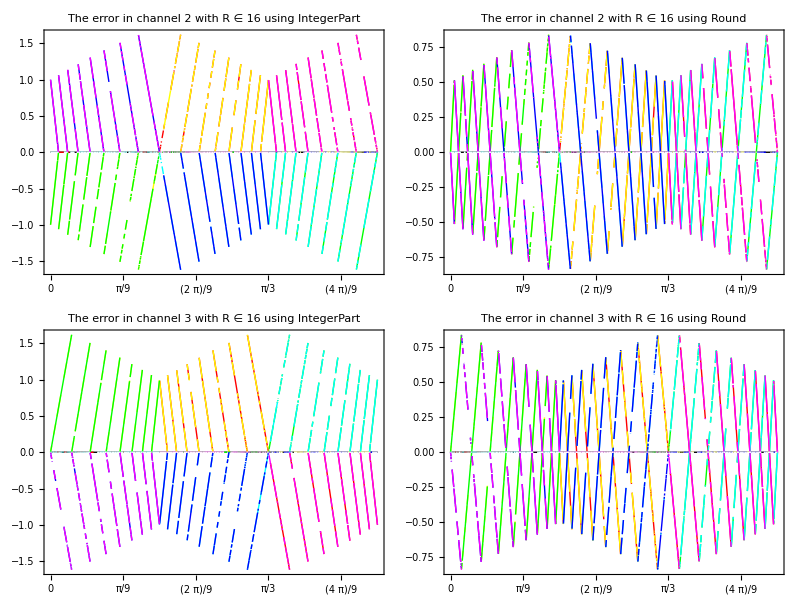

```mathematica
simpleErrorPlot[{0,Pi/2},fRScaledErrorCube,4]
```

The base function for the channel error

```mathematica
2^n (Sin[π/6-θ]-2^(1-n) int[2^(-1+n) Csc[π/6+θ] Sin[π/6-θ]] Sin[π/6+θ]) 2^n (-2^(1-n) Cos[π/6+θ] int[2^(-1+n) Sec[π/6+θ] Sin[θ]]+Sin[θ])
```

```mathematica
errTwo[θ_,n_,int_]:=2^n*((-2^(1 - n))*Cos[Pi/6 + θ]*int[2^(-1 + n)*Sec[Pi/6 + θ]*Sin[θ]] + Sin[θ])
```

```mathematica
errOne[θ_,n_,int_]:=2^n*(Sin[Pi/6 - θ] - 2^(1 - n)*int[2^(-1 + n)*Csc[Pi/6 + θ]*Sin[Pi/6 - θ]]*Sin[Pi/6 + θ]);
```

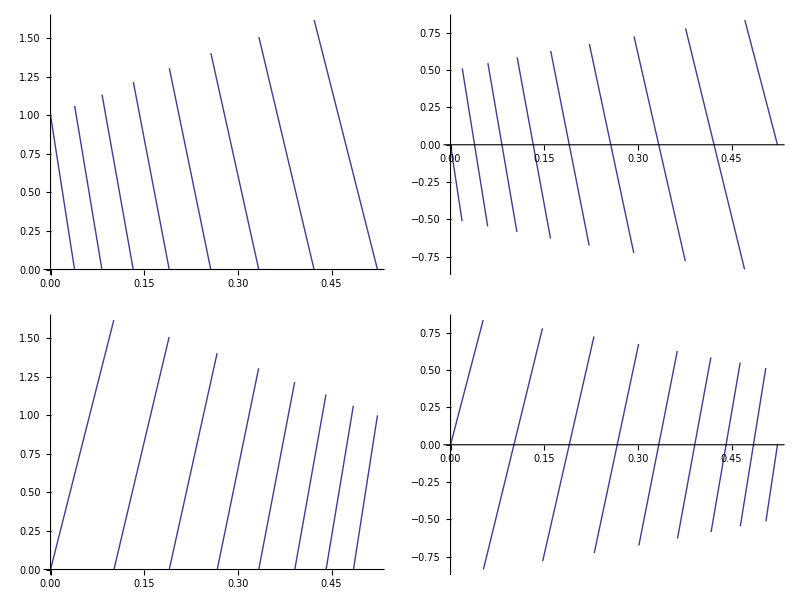

```mathematica
Grid[{{Plot[errOne[θ,4,IntegerPart],{θ,0,Pi/6}],Plot[errOne[θ,4,Round],{θ,0,Pi/6}]},
{Plot[errTwo[θ,4,IntegerPart],{θ,0,Pi/6}],Plot[errTwo[θ,4,Round],{θ,0,Pi/6}]}}]
```

to find the zeros we need to solve

sin(π/6-θ)==2^(1-n) sin(θ+π/6) int(2^(n-1) sin(π/6-θ) csc(θ+π/6))

```mathematica
2^(n-1) sin(π/6-θ) csc(θ+π/6)== int(2^(n-1) sin(π/6-θ) csc(θ+π/6))
```

```mathematica
Simplify[Assuming[Element[θ,Reals]&& θ≥ 0 && θ≤ Pi/6, Solve[y== Csc[π/6+θ] Sin[π/6 - θ],θ]]]
```

{{θ→ConditionalExpression[ArcTan[-(√3 (1+y))/(√(1+y+y^2)),(-1+y)/(√(1+y+y^2))]+2 π C[1],C[1]∈Integers]},{θ→ConditionalExpression[ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))]+2 π C[1],C[1]∈Integers]}}

For a given value of n there are 2^(n - 1) + 1 zeros between 0 and Pi/6

```mathematica
thetaOne[n_]:=Block[{fun},fun[y_]:=ArcTan[(√3 (1+y))/(√(1+y+y^2)),(1-y)/(√(1+y+y^2))];Table[fun[i/(2^(n-1))],{i,2^(n-1),0,-1}]]
thetaTwo[n_]:=Block[{funTwo},funTwo[y_]:=ArcTan[(2+y)/(√(1+y+y^2)),(√3 y)/(√(1+y+y^2))];Table[funTwo[i/(2^(n-1))],{i,0,2^(n-1)}]]
```

```mathematica
nn=4;
setupThetaRanges[nn];
```

The maximum error is given by Sin[θ+π/6] for 0≤ θ≤ Pi/6

```mathematica
maxErrOne[θ_]:=2 Sin[Mod[θ,π/6]+π/6]
maxErrTwo[θ_]:=2 Sin[π/6+Mod[-θ,π/6]]
SetAttributes[maxErrOne,Listable]
SetAttributes[maxErrTwo,Listable]
```

The min and max points are then found by using the values for theta with the max error function

```mathematica
ptsOne[n_]:=Module[{thetaPts},thetaPts=thetaOne[n];{Transpose[{Most[thetaPts],maxErrOne[Most[thetaPts]]}],Transpose[{Rest[thetaPts],Table[0,{i,1,2^(n-1)}]}]}]
ptsTwo[n_]:=Module[{thetaPts},thetaPts=thetaTwo[n];{Transpose[{Most[thetaPts],Table[0,{i,1,2^(n-1)}]}],Transpose[{Rest[thetaPts],maxErrTwo[Rest[thetaPts]]}]}]
```

```mathematica
Clear[plotErrorWithLinesAndPointsOne,plotErrorWithLinesAndPointsTwo];
plotErrorWithLinesAndPointsOne[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsOne[nn];Show[{Plot[{err[θ,nn,IntegerPart],maxErrOne[θ]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
plotErrorWithLinesAndPointsTwo[nn_,color_:{Red,Green},size_:0.02]:=Module[{minMaxPts},minMaxPts=ptsTwo[nn];Show[{Plot[{errTwo[θ,nn,IntegerPart],maxErrTwo[θ]},{θ,0,Pi/6},Ticks->{PiTicks[0,Pi/6,6],All}],ListPlot[minMaxPts[[2]],PlotStyle->{PointSize[size],Darker[color[[1]]]}],ListPlot[minMaxPts[[1]],PlotStyle->{PointSize[size],Darker[color[[2]]]}]}]]
```

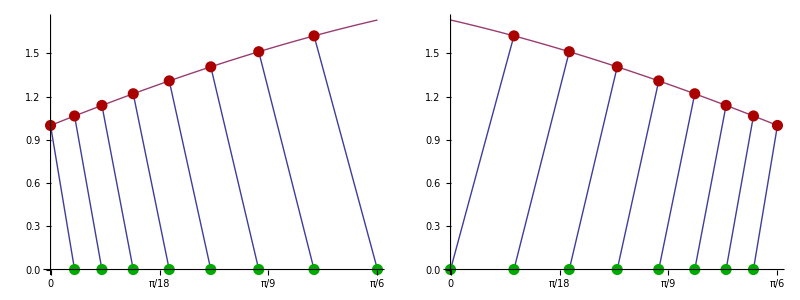

```mathematica
Grid[{{plotErrorWithLinesAndPointsOne[4],plotErrorWithLinesAndPointsTwo[4]}}]
```

We now need to find the intersecting points between the channels.
  To do this we first need to divide up the range into regions where there is only one intersection.

```mathematica
nn=4;
setupThetaRanges[nn];
```

```mathematica
TableForm[{thetaOneVals,thetaTwoVals}]
```

0 | ArcTan[1/(15 √3)] | ArcTan[1/(7 √3)] | ArcTan[(√3)/13] | ArcTan[1/(3 √3)] | ArcTan[5/(11 √3)] | ArcTan[(√3)/5] | ArcTan[7/(9 √3)] | π/6
0 | ArcTan[(√3)/17] | ArcTan[1/(3 √3)] | ArcTan[(3 √3)/19] | ArcTan[(√3)/5] | ArcTan[5/(7 √3)] | ArcTan[(3 √3)/11] | ArcTan[(7 √3)/23] | π/6

in each range we want to find the point of intersection between the errors for this we need to know which of the individual regions we are in for each of the channels.

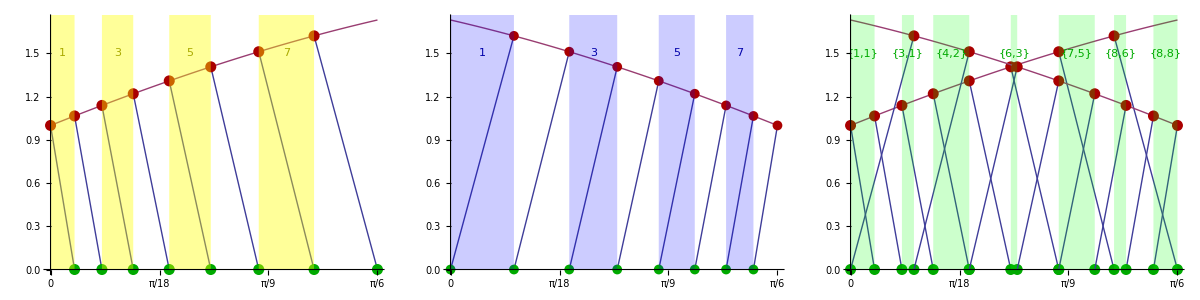

```mathematica
Grid[{{Show[{plotErrorWithLinesAndPointsOne[nn],plotRegionsFromList[thetaOne[nn],Yellow,0.4]}],Show[{plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[thetaTwo[nn],Blue,0.2]}],Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]]}]
}}]
```

in each of the green intersecting regions we need the equatiuon of the lines to find the point of intersection. We use a linear approximation to find the points of intersection.

```mathematica
thetaMidPoints =Map[thetaToPoint,thetaMid];
pts1=ptsOne[nn];
pts2=ptsTwo[nn];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]]
```

{{0.0238288,0.380605},{0.0496731,0.793405},{0.0777568,1.24197},{0.119187,0.301249},{0.150569,0.836795},{0.224585,0.631033},{0.261799,1.31251},{0.299014,0.631033},{0.37303,0.836795},{0.404411,0.301249},{0.445842,1.24197},{0.473926,0.793405},{0.49977,0.380605}}

```mathematica
plotErrorIntersect[nn_,color_:Red,size_:0.02]:=Module[{minMaxPts},
thetaRanges[nn]; pts1=ptsOne[nn];
pts2=ptsTwo[nn];thetaMidPoints=Map[thetaToPoint,thetaMid];
intersect=N[Table[intersectionFromPoints[pts1[[All,thetaMidPoints[[i,1]]]],pts2[[All,thetaMidPoints[[i,2]]]]],{i,1,Length[thetaMidPoints]}]];
ListPlot[intersect,PlotStyle->{PointSize[size],Darker[color]}]]
```

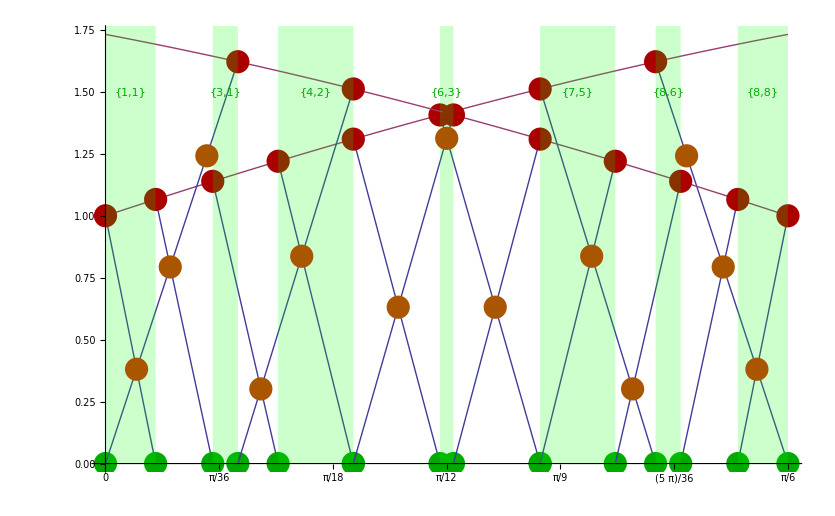

```mathematica
Show[{plotErrorWithLinesAndPointsOne[nn],plotErrorWithLinesAndPointsTwo[nn],plotRegionsFromList[Sort[Union[thetaOne[nn],thetaTwo[nn]],Less],Green,0.2,Map[thetaToPoint,thetaMid]],plotErrorIntersect[nn,Orange]}]
```

## Generating LookupTables

Generate base table

```mathematica
Do[intersect[n]=errorMinTheta[n];Print[StringJoin["Processing : ",ToString[n]]],{n,2,7}]
```

Processing : 2

Processing : 3

Processing : 4

Processing : 5

Processing : 6

Processing : 7

```mathematica
Save[StringJoin[NotebookDirectory[],"errorMinsIntersect.nb"],"intersect"]
```

```mathematica
Get[StringJoin[NotebookDirectory[],"errorMinsIntersect.nb"]];
```

```mathematica
Do[
intersectRound[n]=Map[convRound,intersect[n]];
Print[StringJoin["Processing : ",ToString[n]]],{n,2,12}];
```

Processing : 2

Processing : 3

Processing : 4

Processing : 5

Processing : 6

Processing : 7

Processing : 8

Processing : 9

Processing : 10

Processing : 11

Processing : 12

```mathematica
Clear[thetaGood]
```

```mathematica
Do[
intersectClassified[n]=Map[classifyByNegPowerOfTwo,intersect[n]];
intersectRoundClassified[n]=Map[classifyByNegPowerOfTwo,intersectRound[n]];
thetaGood[1,        n,IntegerPart] = intersectClassified[n][[All,1]];
Do[
thetaGood[2^(-m),    n,IntegerPart]=Extract[thetaGood[1,n,IntegerPart],Position[Map[#> m&,intersectClassified[n][[All,2]]],True]];
thetaGood[2^(-m),    n,Round]=Extract[thetaGood[1,n,IntegerPart],Position[Map[#> m&,intersectRoundClassified[n][[All,2]]],True]];
,{m,1,3}];
Print[StringJoin["Processing : ",ToString[n]]],{n,2,12}]
```

Processing : 2

Processing : 3

Processing : 4

Processing : 5

Processing : 6

Processing : 7

Processing : 8

Processing : 9

Processing : 10

Processing : 11

Processing : 12

```mathematica
Definition[thetaGood]
```

«1»

```mathematica
thetaGood[1/4,7,IntegerPart]
```

{{0,0},{(-ArcTan[1/(63 √3)] ArcTan[1/(43 √3)]+ArcTan[(√3)/125] ArcTan[(√3)/65])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65]),(-ArcTan[1/(43 √3)]+ArcTan[(√3)/125])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65])},{(-ArcTan[5/(123 √3)] ArcTan[(√3)/65]+ArcTan[(√3)/61] ArcTan[(3 √3)/131])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131]),(-ArcTan[(√3)/65]+ArcTan[(√3)/61])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131])},{(-ArcTan[1/(15 √3)] ArcTan[(3 √3)/131]+ArcTan[1/(11 √3)] ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119]),(-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])},{(-ArcTan[5/(59 √3)] ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)] ArcTan[(5 √3)/133])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133]),(-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133])},{(-ArcTan[(√3)/29] ArcTan[(5 √3)/133]+ArcTan[13/(115 √3)] ArcTan[(3 √3)/67])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67]),(ArcTan[13/(115 √3)]-ArcTan[(5 √3)/133])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67])},{(-ArcTan[11/(53 √3)] ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)] ArcTan[(11 √3)/139])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139]),(-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139])},{(-ArcTan[(√3)/13] ArcTan[(11 √3)/139]+ArcTan[25/(103 √3)] ArcTan[(3 √3)/35])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35]),(ArcTan[25/(103 √3)]-ArcTan[(11 √3)/139])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35])},{(-ArcTan[13/(47 √3)] ArcTan[(9 √3)/101]+ArcTan[7/(25 √3)] ArcTan[(7 √3)/71])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71]),(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71])},{(ArcTan[31/(97 √3)] ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49] ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143]),(ArcTan[31/(97 √3)]-ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143])},{ArcTan[1/(3 √3)],0},{(ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]-ArcTan[17/(47 √3)] ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73]),(ArcTan[35/(93 √3)]-ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73])},{(-ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23] ArcTan[(5 √3)/37])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37]),(-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37])},{(-ArcTan[(3 √3)/23] ArcTan[(5 √3)/37]+ArcTan[37/(91 √3)] ArcTan[(21 √3)/149])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149]),(ArcTan[37/(91 √3)]-ArcTan[(5 √3)/37])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149])},{(ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]-ArcTan[43/(85 √3)] ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155]),(ArcTan[11/(21 √3)]-ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155])},{(-ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83] ArcTan[(29 √3)/157])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157]),(-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157])},{(-ArcTan[(15 √3)/83] ArcTan[(29 √3)/157]+ArcTan[23/(41 √3)] ArcTan[(15 √3)/79])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79]),(ArcTan[23/(41 √3)]-ArcTan[(29 √3)/157])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79])},{ArcTan[(√3)/5],0},{(ArcTan[49/(79 √3)] ArcTan[17/(27 √3)]-ArcTan[(√3)/5] ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161]),(ArcTan[49/(79 √3)]-ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161])},{(-ArcTan[25/(39 √3)] ArcTan[(9 √3)/41]+ArcTan[37/(55 √3)] ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77]),(-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])},{(ArcTan[53/(75 √3)] ArcTan[5/(7 √3)]-ArcTan[13/(19 √3)] ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167]),(ArcTan[53/(75 √3)]-ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167])},{(-ArcTan[53/(75 √3)] ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37] ArcTan[(21 √3)/85])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85]),(-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85])},{(ArcTan[59/(69 √3)] ArcTan[13/(15 √3)]-ArcTan[29/(35 √3)] ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179]),(ArcTan[59/(69 √3)]-ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179])},{(-ArcTan[59/(69 √3)] ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17] ArcTan[(27 √3)/91])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91]),(-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91])},{(-ArcTan[55/(61 √3)] ArcTan[(5 √3)/17]+ArcTan[61/(67 √3)] ArcTan[(7 √3)/23])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23]),(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23])},{(-ArcTan[61/(67 √3)] ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)] ArcTan[(59 √3)/187])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187]),(-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187])},{(-ArcTan[31/(33 √3)] ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65] ArcTan[(31 √3)/95])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95]),(-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95])},{π/6,0}}

```mathematica
thetaGood[1/2,7,IntegerPart]
```

{{0,0},{(ArcTan[1/(127 √3)] ArcTan[1/(43 √3)])/(ArcTan[1/(127 √3)]+ArcTan[1/(43 √3)]),ArcTan[1/(127 √3)]/(ArcTan[1/(127 √3)]+ArcTan[1/(43 √3)])},{(-ArcTan[1/(63 √3)] ArcTan[1/(43 √3)]+ArcTan[(√3)/125] ArcTan[(√3)/65])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65]),(-ArcTan[1/(43 √3)]+ArcTan[(√3)/125])/(-ArcTan[1/(63 √3)]-ArcTan[1/(43 √3)]+ArcTan[(√3)/125]+ArcTan[(√3)/65])},{(-ArcTan[1/(43 √3)] ArcTan[(√3)/125]+ArcTan[1/(31 √3)] ArcTan[(√3)/65])/(-ArcTan[1/(43 √3)]+ArcTan[1/(31 √3)]-ArcTan[(√3)/125]+ArcTan[(√3)/65]),(-ArcTan[1/(43 √3)]+ArcTan[1/(31 √3)])/(-ArcTan[1/(43 √3)]+ArcTan[1/(31 √3)]-ArcTan[(√3)/125]+ArcTan[(√3)/65])},{(-ArcTan[5/(123 √3)] ArcTan[(√3)/65]+ArcTan[(√3)/61] ArcTan[(3 √3)/131])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131]),(-ArcTan[(√3)/65]+ArcTan[(√3)/61])/(-ArcTan[5/(123 √3)]-ArcTan[(√3)/65]+ArcTan[(√3)/61]+ArcTan[(3 √3)/131])},{(-ArcTan[(√3)/65] ArcTan[(√3)/61]+ArcTan[7/(121 √3)] ArcTan[(3 √3)/131])/(ArcTan[7/(121 √3)]-ArcTan[(√3)/65]-ArcTan[(√3)/61]+ArcTan[(3 √3)/131]),(ArcTan[7/(121 √3)]-ArcTan[(√3)/65])/(ArcTan[7/(121 √3)]-ArcTan[(√3)/65]-ArcTan[(√3)/61]+ArcTan[(3 √3)/131])},{(-ArcTan[1/(15 √3)] ArcTan[(3 √3)/131]+ArcTan[1/(11 √3)] ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119]),(-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])/(-ArcTan[1/(15 √3)]+ArcTan[1/(11 √3)]-ArcTan[(3 √3)/131]+ArcTan[(3 √3)/119])},{(-ArcTan[5/(59 √3)] ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)] ArcTan[(5 √3)/133])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133]),(-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)])/(-ArcTan[5/(59 √3)]-ArcTan[1/(11 √3)]+ArcTan[11/(117 √3)]+ArcTan[(5 √3)/133])},{(-ArcTan[1/(11 √3)] ArcTan[11/(117 √3)]+ArcTan[(√3)/29] ArcTan[(5 √3)/133])/(-ArcTan[1/(11 √3)]-ArcTan[11/(117 √3)]+ArcTan[(√3)/29]+ArcTan[(5 √3)/133]),(-ArcTan[1/(11 √3)]+ArcTan[(√3)/29])/(-ArcTan[1/(11 √3)]-ArcTan[11/(117 √3)]+ArcTan[(√3)/29]+ArcTan[(5 √3)/133])},{(-ArcTan[(√3)/29] ArcTan[(5 √3)/133]+ArcTan[13/(115 √3)] ArcTan[(3 √3)/67])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67]),(ArcTan[13/(115 √3)]-ArcTan[(5 √3)/133])/(ArcTan[13/(115 √3)]-ArcTan[(√3)/29]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67])},{(-ArcTan[13/(115 √3)] ArcTan[(5 √3)/133]+ArcTan[7/(57 √3)] ArcTan[(3 √3)/67])/(-ArcTan[13/(115 √3)]+ArcTan[7/(57 √3)]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67]),(ArcTan[7/(57 √3)]-ArcTan[(5 √3)/133])/(-ArcTan[13/(115 √3)]+ArcTan[7/(57 √3)]-ArcTan[(5 √3)/133]+ArcTan[(3 √3)/67])},{(ArcTan[1/(7 √3)] ArcTan[7/(45 √3)]-ArcTan[(5 √3)/113] ArcTan[(3 √3)/67])/(ArcTan[1/(7 √3)]+ArcTan[7/(45 √3)]-ArcTan[(5 √3)/113]-ArcTan[(3 √3)/67]),(ArcTan[1/(7 √3)]-ArcTan[(3 √3)/67])/(ArcTan[1/(7 √3)]+ArcTan[7/(45 √3)]-ArcTan[(5 √3)/113]-ArcTan[(3 √3)/67])},{(-ArcTan[17/(111 √3)] ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55] ArcTan[(√3)/17])/(-ArcTan[17/(111 √3)]-ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55]+ArcTan[(√3)/17]),(-ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55])/(-ArcTan[17/(111 √3)]-ArcTan[7/(45 √3)]+ArcTan[(3 √3)/55]+ArcTan[(√3)/17])},{(-ArcTan[19/(109 √3)] ArcTan[(√3)/17]+ArcTan[5/(27 √3)] ArcTan[(9 √3)/137])/(-ArcTan[19/(109 √3)]+ArcTan[5/(27 √3)]-ArcTan[(√3)/17]+ArcTan[(9 √3)/137]),(ArcTan[5/(27 √3)]-ArcTan[(√3)/17])/(-ArcTan[19/(109 √3)]+ArcTan[5/(27 √3)]-ArcTan[(√3)/17]+ArcTan[(9 √3)/137])},{(ArcTan[11/(53 √3)] ArcTan[5/(23 √3)]-ArcTan[(7 √3)/107] ArcTan[(9 √3)/137])/(ArcTan[11/(53 √3)]+ArcTan[5/(23 √3)]-ArcTan[(7 √3)/107]-ArcTan[(9 √3)/137]),(ArcTan[11/(53 √3)]-ArcTan[(9 √3)/137])/(ArcTan[11/(53 √3)]+ArcTan[5/(23 √3)]-ArcTan[(7 √3)/107]-ArcTan[(9 √3)/137])},{(-ArcTan[11/(53 √3)] ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)] ArcTan[(11 √3)/139])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139]),(-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)])/(-ArcTan[11/(53 √3)]-ArcTan[5/(23 √3)]+ArcTan[23/(105 √3)]+ArcTan[(11 √3)/139])},{(-ArcTan[5/(23 √3)] ArcTan[23/(105 √3)]+ArcTan[(√3)/13] ArcTan[(11 √3)/139])/(-ArcTan[5/(23 √3)]-ArcTan[23/(105 √3)]+ArcTan[(√3)/13]+ArcTan[(11 √3)/139]),(-ArcTan[5/(23 √3)]+ArcTan[(√3)/13])/(-ArcTan[5/(23 √3)]-ArcTan[23/(105 √3)]+ArcTan[(√3)/13]+ArcTan[(11 √3)/139])},{(-ArcTan[(√3)/13] ArcTan[(11 √3)/139]+ArcTan[25/(103 √3)] ArcTan[(3 √3)/35])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35]),(ArcTan[25/(103 √3)]-ArcTan[(11 √3)/139])/(ArcTan[25/(103 √3)]-ArcTan[(√3)/13]-ArcTan[(11 √3)/139]+ArcTan[(3 √3)/35])},{(-ArcTan[13/(51 √3)] ArcTan[(3 √3)/35]+ArcTan[13/(47 √3)] ArcTan[(9 √3)/101])/(-ArcTan[13/(51 √3)]+ArcTan[13/(47 √3)]-ArcTan[(3 √3)/35]+ArcTan[(9 √3)/101]),(-ArcTan[(3 √3)/35]+ArcTan[(9 √3)/101])/(-ArcTan[13/(51 √3)]+ArcTan[13/(47 √3)]-ArcTan[(3 √3)/35]+ArcTan[(9 √3)/101])},{(-ArcTan[13/(47 √3)] ArcTan[(9 √3)/101]+ArcTan[7/(25 √3)] ArcTan[(7 √3)/71])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71]),(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)])/(-ArcTan[13/(47 √3)]+ArcTan[7/(25 √3)]-ArcTan[(9 √3)/101]+ArcTan[(7 √3)/71])},{(-ArcTan[29/(99 √3)] ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49] ArcTan[(15 √3)/143])/(-ArcTan[29/(99 √3)]-ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49]+ArcTan[(15 √3)/143]),(-ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49])/(-ArcTan[29/(99 √3)]-ArcTan[(7 √3)/71]+ArcTan[(5 √3)/49]+ArcTan[(15 √3)/143])},{(ArcTan[31/(97 √3)] ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49] ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143]),(ArcTan[31/(97 √3)]-ArcTan[(15 √3)/143])/(ArcTan[31/(97 √3)]+ArcTan[1/(3 √3)]-ArcTan[(5 √3)/49]-ArcTan[(15 √3)/143])},{ArcTan[1/(3 √3)],0},{(-ArcTan[1/(3 √3)]^2+ArcTan[(11 √3)/95] ArcTan[(17 √3)/145])/(-2 ArcTan[1/(3 √3)]+ArcTan[(11 √3)/95]+ArcTan[(17 √3)/145]),(-ArcTan[1/(3 √3)]+ArcTan[(11 √3)/95])/(-2 ArcTan[1/(3 √3)]+ArcTan[(11 √3)/95]+ArcTan[(17 √3)/145])},{(-ArcTan[(11 √3)/95] ArcTan[(17 √3)/145]+ArcTan[17/(47 √3)] ArcTan[(9 √3)/73])/(ArcTan[17/(47 √3)]-ArcTan[(11 √3)/95]-ArcTan[(17 √3)/145]+ArcTan[(9 √3)/73]),(ArcTan[17/(47 √3)]-ArcTan[(17 √3)/145])/(ArcTan[17/(47 √3)]-ArcTan[(11 √3)/95]-ArcTan[(17 √3)/145]+ArcTan[(9 √3)/73])},{(ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]-ArcTan[17/(47 √3)] ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73]),(ArcTan[35/(93 √3)]-ArcTan[(9 √3)/73])/(-ArcTan[17/(47 √3)]+ArcTan[35/(93 √3)]+ArcTan[19/(49 √3)]-ArcTan[(9 √3)/73])},{(-ArcTan[35/(93 √3)] ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23] ArcTan[(5 √3)/37])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37]),(-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23])/(-ArcTan[35/(93 √3)]-ArcTan[19/(49 √3)]+ArcTan[(3 √3)/23]+ArcTan[(5 √3)/37])},{(-ArcTan[(3 √3)/23] ArcTan[(5 √3)/37]+ArcTan[37/(91 √3)] ArcTan[(21 √3)/149])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149]),(ArcTan[37/(91 √3)]-ArcTan[(5 √3)/37])/(ArcTan[37/(91 √3)]-ArcTan[(3 √3)/23]-ArcTan[(5 √3)/37]+ArcTan[(21 √3)/149])},{(-ArcTan[19/(45 √3)] ArcTan[(21 √3)/149]+ArcTan[11/(25 √3)] ArcTan[(13 √3)/89])/(-ArcTan[19/(45 √3)]+ArcTan[11/(25 √3)]-ArcTan[(21 √3)/149]+ArcTan[(13 √3)/89]),(-ArcTan[(21 √3)/149]+ArcTan[(13 √3)/89])/(-ArcTan[19/(45 √3)]+ArcTan[11/(25 √3)]-ArcTan[(21 √3)/149]+ArcTan[(13 √3)/89])},{(-ArcTan[11/(25 √3)] ArcTan[(13 √3)/89]+ArcTan[5/(11 √3)] ArcTan[(23 √3)/151])/(-ArcTan[11/(25 √3)]+ArcTan[5/(11 √3)]-ArcTan[(13 √3)/89]+ArcTan[(23 √3)/151]),(-ArcTan[11/(25 √3)]+ArcTan[5/(11 √3)])/(-ArcTan[11/(25 √3)]+ArcTan[5/(11 √3)]-ArcTan[(13 √3)/89]+ArcTan[(23 √3)/151])},{(-ArcTan[5/(11 √3)] ArcTan[(23 √3)/151]+ArcTan[41/(87 √3)] ArcTan[(3 √3)/19])/(-ArcTan[5/(11 √3)]+ArcTan[41/(87 √3)]-ArcTan[(23 √3)/151]+ArcTan[(3 √3)/19]),(ArcTan[41/(87 √3)]-ArcTan[(23 √3)/151])/(-ArcTan[5/(11 √3)]+ArcTan[41/(87 √3)]-ArcTan[(23 √3)/151]+ArcTan[(3 √3)/19])},{(-ArcTan[41/(87 √3)] ArcTan[(3 √3)/19]+ArcTan[25/(51 √3)] ArcTan[(7 √3)/43])/(-ArcTan[41/(87 √3)]+ArcTan[25/(51 √3)]-ArcTan[(3 √3)/19]+ArcTan[(7 √3)/43]),(-ArcTan[(3 √3)/19]+ArcTan[(7 √3)/43])/(-ArcTan[41/(87 √3)]+ArcTan[25/(51 √3)]-ArcTan[(3 √3)/19]+ArcTan[(7 √3)/43])},{(-ArcTan[25/(51 √3)] ArcTan[(7 √3)/43]+ArcTan[43/(85 √3)] ArcTan[(13 √3)/77])/(-ArcTan[25/(51 √3)]+ArcTan[43/(85 √3)]-ArcTan[(7 √3)/43]+ArcTan[(13 √3)/77]),(-ArcTan[25/(51 √3)]+ArcTan[43/(85 √3)])/(-ArcTan[25/(51 √3)]+ArcTan[43/(85 √3)]-ArcTan[(7 √3)/43]+ArcTan[(13 √3)/77])},{(ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]-ArcTan[43/(85 √3)] ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155]),(ArcTan[11/(21 √3)]-ArcTan[(27 √3)/155])/(-ArcTan[43/(85 √3)]+ArcTan[11/(21 √3)]+ArcTan[7/(13 √3)]-ArcTan[(27 √3)/155])},{(-ArcTan[11/(21 √3)] ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83] ArcTan[(29 √3)/157])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157]),(-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83])/(-ArcTan[11/(21 √3)]-ArcTan[7/(13 √3)]+ArcTan[(15 √3)/83]+ArcTan[(29 √3)/157])},{(-ArcTan[(15 √3)/83] ArcTan[(29 √3)/157]+ArcTan[23/(41 √3)] ArcTan[(15 √3)/79])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79]),(ArcTan[23/(41 √3)]-ArcTan[(29 √3)/157])/(ArcTan[23/(41 √3)]-ArcTan[(15 √3)/83]-ArcTan[(29 √3)/157]+ArcTan[(15 √3)/79])},{(ArcTan[47/(81 √3)] ArcTan[31/(53 √3)]-ArcTan[23/(41 √3)] ArcTan[(15 √3)/79])/(-ArcTan[23/(41 √3)]+ArcTan[47/(81 √3)]+ArcTan[31/(53 √3)]-ArcTan[(15 √3)/79]),(ArcTan[47/(81 √3)]-ArcTan[(15 √3)/79])/(-ArcTan[23/(41 √3)]+ArcTan[47/(81 √3)]+ArcTan[31/(53 √3)]-ArcTan[(15 √3)/79])},{(-ArcTan[47/(81 √3)] ArcTan[31/(53 √3)]+ArcTan[(√3)/5]^2)/(-ArcTan[47/(81 √3)]-ArcTan[31/(53 √3)]+2 ArcTan[(√3)/5]),(-ArcTan[31/(53 √3)]+ArcTan[(√3)/5])/(-ArcTan[47/(81 √3)]-ArcTan[31/(53 √3)]+2 ArcTan[(√3)/5])},{ArcTan[(√3)/5],0},{(ArcTan[49/(79 √3)] ArcTan[17/(27 √3)]-ArcTan[(√3)/5] ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161]),(ArcTan[49/(79 √3)]-ArcTan[(33 √3)/161])/(ArcTan[49/(79 √3)]+ArcTan[17/(27 √3)]-ArcTan[(√3)/5]-ArcTan[(33 √3)/161])},{(-ArcTan[49/(79 √3)] ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)] ArcTan[(35 √3)/163])/(-ArcTan[49/(79 √3)]-ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)]+ArcTan[(35 √3)/163]),(-ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)])/(-ArcTan[49/(79 √3)]-ArcTan[17/(27 √3)]+ArcTan[25/(39 √3)]+ArcTan[(35 √3)/163])},{(-ArcTan[25/(39 √3)] ArcTan[(9 √3)/41]+ArcTan[37/(55 √3)] ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77]),(-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])/(-ArcTan[25/(39 √3)]+ArcTan[37/(55 √3)]-ArcTan[(9 √3)/41]+ArcTan[(17 √3)/77])},{(-ArcTan[37/(55 √3)] ArcTan[(17 √3)/77]+ArcTan[13/(19 √3)] ArcTan[(19 √3)/83])/(-ArcTan[37/(55 √3)]+ArcTan[13/(19 √3)]-ArcTan[(17 √3)/77]+ArcTan[(19 √3)/83]),(-ArcTan[37/(55 √3)]+ArcTan[13/(19 √3)])/(-ArcTan[37/(55 √3)]+ArcTan[13/(19 √3)]-ArcTan[(17 √3)/77]+ArcTan[(19 √3)/83])},{(ArcTan[53/(75 √3)] ArcTan[5/(7 √3)]-ArcTan[13/(19 √3)] ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167]),(ArcTan[53/(75 √3)]-ArcTan[(39 √3)/167])/(-ArcTan[13/(19 √3)]+ArcTan[53/(75 √3)]+ArcTan[5/(7 √3)]-ArcTan[(39 √3)/167])},{(-ArcTan[53/(75 √3)] ArcTan[5/(7 √3)]+ArcTan[(41 √3)/169] ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[5/(7 √3)]+ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]),(-ArcTan[5/(7 √3)]+ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[5/(7 √3)]+ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37])},{(-ArcTan[53/(75 √3)] ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37] ArcTan[(21 √3)/85])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85]),(-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37])/(-ArcTan[53/(75 √3)]-ArcTan[(41 √3)/169]+ArcTan[(9 √3)/37]+ArcTan[(21 √3)/85])},{(ArcTan[55/(73 √3)] ArcTan[43/(57 √3)]-ArcTan[(9 √3)/37] ArcTan[(21 √3)/85])/(ArcTan[55/(73 √3)]+ArcTan[43/(57 √3)]-ArcTan[(9 √3)/37]-ArcTan[(21 √3)/85]),(ArcTan[55/(73 √3)]-ArcTan[(21 √3)/85])/(ArcTan[55/(73 √3)]+ArcTan[43/(57 √3)]-ArcTan[(9 √3)/37]-ArcTan[(21 √3)/85])},{(-ArcTan[55/(73 √3)] ArcTan[(11 √3)/43]+ArcTan[7/(9 √3)] ArcTan[(45 √3)/173])/(-ArcTan[55/(73 √3)]+ArcTan[7/(9 √3)]-ArcTan[(11 √3)/43]+ArcTan[(45 √3)/173]),(ArcTan[7/(9 √3)]-ArcTan[(11 √3)/43])/(-ArcTan[55/(73 √3)]+ArcTan[7/(9 √3)]-ArcTan[(11 √3)/43]+ArcTan[(45 √3)/173])},{(-ArcTan[7/(9 √3)] ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71] ArcTan[(47 √3)/175])/(-ArcTan[7/(9 √3)]-ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71]+ArcTan[(47 √3)/175]),(-ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71])/(-ArcTan[7/(9 √3)]-ArcTan[23/(29 √3)]+ArcTan[(19 √3)/71]+ArcTan[(47 √3)/175])},{(ArcTan[29/(35 √3)] ArcTan[49/(59 √3)]-ArcTan[(19 √3)/71] ArcTan[(3 √3)/11])/(ArcTan[29/(35 √3)]+ArcTan[49/(59 √3)]-ArcTan[(19 √3)/71]-ArcTan[(3 √3)/11]),(ArcTan[29/(35 √3)]-ArcTan[(3 √3)/11])/(ArcTan[29/(35 √3)]+ArcTan[49/(59 √3)]-ArcTan[(19 √3)/71]-ArcTan[(3 √3)/11])},{(-ArcTan[29/(35 √3)] ArcTan[(25 √3)/89]+ArcTan[59/(69 √3)] ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]-ArcTan[(25 √3)/89]+ArcTan[(51 √3)/179]),(ArcTan[59/(69 √3)]-ArcTan[(25 √3)/89])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]-ArcTan[(25 √3)/89]+ArcTan[(51 √3)/179])},{(ArcTan[59/(69 √3)] ArcTan[13/(15 √3)]-ArcTan[29/(35 √3)] ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179]),(ArcTan[59/(69 √3)]-ArcTan[(51 √3)/179])/(-ArcTan[29/(35 √3)]+ArcTan[59/(69 √3)]+ArcTan[13/(15 √3)]-ArcTan[(51 √3)/179])},{(-ArcTan[59/(69 √3)] ArcTan[13/(15 √3)]+ArcTan[(53 √3)/181] ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[13/(15 √3)]+ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]),(-ArcTan[13/(15 √3)]+ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[13/(15 √3)]+ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17])},{(-ArcTan[59/(69 √3)] ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17] ArcTan[(27 √3)/91])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91]),(-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17])/(-ArcTan[59/(69 √3)]-ArcTan[(53 √3)/181]+ArcTan[(5 √3)/17]+ArcTan[(27 √3)/91])},{(-ArcTan[55/(61 √3)] ArcTan[(5 √3)/17]+ArcTan[61/(67 √3)] ArcTan[(7 √3)/23])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23]),(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)])/(-ArcTan[55/(61 √3)]+ArcTan[61/(67 √3)]-ArcTan[(5 √3)/17]+ArcTan[(7 √3)/23])},{(ArcTan[29/(31 √3)] ArcTan[31/(33 √3)]-ArcTan[61/(67 √3)] ArcTan[(57 √3)/185])/(-ArcTan[61/(67 √3)]+ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]-ArcTan[(57 √3)/185]),(ArcTan[31/(33 √3)]-ArcTan[(57 √3)/185])/(-ArcTan[61/(67 √3)]+ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]-ArcTan[(57 √3)/185])},{(-ArcTan[61/(67 √3)] ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)] ArcTan[(59 √3)/187])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187]),(-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)])/(-ArcTan[61/(67 √3)]-ArcTan[29/(31 √3)]+ArcTan[31/(33 √3)]+ArcTan[(59 √3)/187])},{(-ArcTan[31/(33 √3)] ArcTan[(15 √3)/47]+ArcTan[61/(63 √3)] ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]+ArcTan[61/(63 √3)]-ArcTan[(15 √3)/47]+ArcTan[(21 √3)/65]),(-ArcTan[(15 √3)/47]+ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]+ArcTan[61/(63 √3)]-ArcTan[(15 √3)/47]+ArcTan[(21 √3)/65])},{(-ArcTan[31/(33 √3)] ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65] ArcTan[(31 √3)/95])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95]),(-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65])/(-ArcTan[31/(33 √3)]-ArcTan[61/(63 √3)]+ArcTan[(21 √3)/65]+ArcTan[(31 √3)/95])},{(π^2/36-ArcTan[(21 √3)/65] ArcTan[(63 √3)/191])/(π/3-ArcTan[(21 √3)/65]-ArcTan[(63 √3)/191]),(π/6-ArcTan[(63 √3)/191])/(π/3-ArcTan[(21 √3)/65]-ArcTan[(63 √3)/191])},{π/6,0}}

```mathematica
Save[StringJoin[NotebookDirectory[],"errorMinsThetaGood.nb"],"thetaGood"];
```

```mathematica
Get[StringJoin[NotebookDirectory[],"errorMinsThetaGood.nb"]];
```

```mathematica
nearestMinPos[θ_,list_:thetaGood[1/2,7,IntegerPart][[All,1]]]:=Module[{},Ordering[Map[Abs[(#- {Mod[θ,Pi/6],0})[[1]]]&,list],{1}][[1]]];
nearestMin[θ_,list_:thetaGood[1/2,7,IntegerPart][[All,1]]]:=Module[{pos},pos = nearestMinPos[θ,list];{Quotient[θ,Pi/6] Pi/6,0} + list[[pos]]]
```

```mathematica
CFormTable[list_]:= Map[NumberForm[#,{18,17},NumberPadding->{"","0"}]& , N[list]]
```

```mathematica
CFormTable[thetaGood[1/2,7,IntegerPart][[All,1]]]
```

{0.00000000000000000,0.00339610895840325,0.01374296917365025,0.01724464584534448,0.02790727543575958,0.03151377567696647,0.04248882730150490,0.05369461752341520,0.05748045247612755,0.06512688625498292,0.06898705947201238,0.08071271726878000,0.09265048012254600,0.10479218393140060,0.11712842403107090,0.12545545119752160,0.12964854674490860,0.13809161804831330,0.15089117030593700,0.15950815616425560,0.17254856891055130,0.18131200163770730,0.19012560334646680,0.19454962577344720,0.20342886698336310,0.21234524551290230,0.22129329080903410,0.23026741212248330,0.24376501627352540,0.25277926823047870,0.26179938779914920,0.27081950736782060,0.27983375932477350,0.29333136347581540,0.30230548478926350,0.31125353008539700,0.32016990861493610,0.32904914982485260,0.33347317225183210,0.34228677396059250,0.35105020668774720,0.36409061943404270,0.37270760529236310,0.38550715754998620,0.39395022885338900,0.39814332440077680,0.40647035156722690,0.41880659166689710,0.43094829547575220,0.44288605832951710,0.45461171612628630,0.45847188934331640,0.46611832312217190,0.46990415807488140,0.48110994829679400,0.49208499992133210,0.49569150016254310,0.50635412975295500,0.50985580642464540,0.52020266663989880,0.52359877559829880}

## Testing the Approximation

For color in a 2^n unsigned representation we desire to represent the rotation in such a way that the rotaed space is in 2^(2n). 
To this end the rotation must be in 2^(n-2)signed. Using the factored representation we can gain 1 bit to give 2^(n-1)signed.

```mathematica
colorMat[mat_,positive_:Red,neg_:Blue,different_:Framed]:=Module[{pos,out}, 
pos=Position[Sign[mat],1];out=MapAt[Style[#,positive]&,mat,pos]; 
pos=Position[Sign[mat],-1];out=MapAt[Style[#,neg]&,out,pos];
pos=Position[matSameSign[mat],0];out=MapAt[different[#]&,out,pos];
 out];
```

```mathematica
Clear[gridPrint]
gridPrint[fun_,form_:Identity]:={Style[HoldForm[fun],Bold],mForm[form[colorMat[fun]]]}
SetAttributes[gridPrint,HoldFirst]
```

```mathematica
Clear[approxReport];
approxReport[θ_,n_,round_:IntegerPart]:=Block[{qR,aR,nR,error,ptsError,aRnRGrid,aRnRError,minMaxError,errLimits,thetastr},
qR=round[fR[θ,2^(n-1)]];
aR = nRScale[θ] rRScale fRScale[θ,2^(n-1)] qR;
nR=nRScale[θ] rRScale rR[θ];
wrkBits=Ceiling[N[Log[Max[(qR.((2^n)RGBCube))]]/Log[2]]];
aRnRGrid=Grid[{Sequence@@Transpose[{
gridPrint[nRScale[θ]],gridPrint[rRScale],gridPrint[fRScale[θ,2^(n-1)]],gridPrint[qR],gridPrint[aR,NumberForm[#,{5,4}]&]}],
Sequence@@Transpose[{gridPrint[nRScale[θ]],gridPrint[rRScale],gridPrint[rR[θ],NumberForm[#,{5,4}]&],{SpanFromLeft,SpanFromLeft},gridPrint[nR,NumberForm[#,{5,4}]&]}]}
,Alignment->Center, Frame -> All,Spacings-> 1,Background->{None,{LightGreen,None,LightGreen,None}}];
error = aR-nR;
ptsError = 2^n error . RGBCube;
minMaxError = Map[{Min[#],Max[#]}&,Threshold[ptsError],1];
errLimits=Row[{mForm[Transpose[minMaxError][[1]]]," < (aR - nR) . ",mForm[2^n RGBCube]," < ",mForm[Transpose[minMaxError][[2]]]}];
aRnRError=Column[gridPrint[(aR-nR)2^n],Center, Frame -> All,Spacings-> 1,Background->{LightGreen,None}];
thetastr = StringJoin["θ = ",ToString[θ,TraditionalForm]];
Panel[Grid[{{aRnRGrid,SpanFromLeft},{aRnRError,errLimits}}],{thetastr},{Top}]]
```

```mathematica
tG=N[thetaGood[1,8-1,IntegerPart][[All,1]]]
```

{0.,0.00339611,0.00681868,0.0102676,0.013743,0.0172446,0.0207727,0.0243269,0.0279073,0.0315138,0.0351463,0.0388047,0.0424888,0.0461987,0.049934,0.0536946,0.0574805,0.0612913,0.0651269,0.0689871,0.0728716,0.0767802,0.0807127,0.0846688,0.0886482,0.0926505,0.0966755,0.100723,0.104792,0.108883,0.112995,0.117128,0.121282,0.125455,0.129649,0.133861,0.138092,0.142341,0.146607,0.150891,0.155192,0.159508,0.16384,0.168187,0.172549,0.176924,0.181312,0.185713,0.190126,0.19455,0.198984,0.203429,0.207883,0.212345,0.216816,0.221293,0.225777,0.230267,0.234762,0.239262,0.243765,0.248271,0.252779,0.257289,0.261799,0.26631,0.27082,0.275328,0.279834,0.284337,0.288836,0.293331,0.297821,0.302305,0.306783,0.311254,0.315716,0.32017,0.324614,0.329049,0.333473,0.337886,0.342287,0.346675,0.35105,0.355412,0.359759,0.364091,0.368407,0.372708,0.376991,0.381258,0.385507,0.389738,0.39395,0.398143,0.402317,0.40647,0.410603,0.414716,0.418807,0.422876,0.426923,0.430948,0.434951,0.43893,0.442886,0.446819,0.450727,0.454612,0.458472,0.462307,0.466118,0.469904,0.473665,0.4774,0.48111,0.484794,0.488452,0.492085,0.495692,0.499272,0.502826,0.506354,0.509856,0.513331,0.51678,0.520203,0.523599}

```mathematica
tB=(Most[tG]+Rest[tG])/2;
```

```mathematica
thetaBad=Union[tG,tB];
```

```mathematica
thetaBad=Sort[N[thetaBad]]
```

{0.,0.00169805,0.00339611,0.00510739,0.00681868,0.00854316,0.0102676,0.0120053,0.013743,0.0154938,0.0172446,0.0190087,0.0207727,0.0225498,0.0243269,0.0261171,0.0279073,0.0297105,0.0315138,0.03333,0.0351463,0.0369755,0.0388047,0.0406468,0.0424888,0.0443437,0.0461987,0.0480663,0.049934,0.0518143,0.0536946,0.0555875,0.0574805,0.0593859,0.0612913,0.0632091,0.0651269,0.067057,0.0689871,0.0709293,0.0728716,0.0748259,0.0767802,0.0787465,0.0807127,0.0826908,0.0846688,0.0866585,0.0886482,0.0906493,0.0926505,0.094663,0.0966755,0.0986992,0.100723,0.102758,0.104792,0.106838,0.108883,0.110939,0.112995,0.115062,0.117128,0.119205,0.121282,0.123369,0.125455,0.127552,0.129649,0.131755,0.133861,0.135976,0.138092,0.140216,0.142341,0.144474,0.146607,0.148749,0.150891,0.153041,0.155192,0.15735,0.159508,0.161674,0.16384,0.166014,0.168187,0.170368,0.172549,0.174736,0.176924,0.179118,0.181312,0.183512,0.185713,0.187919,0.190126,0.192338,0.19455,0.196767,0.198984,0.201207,0.203429,0.205656,0.207883,0.210114,0.212345,0.21458,0.216816,0.219054,0.221293,0.223535,0.225777,0.228022,0.230267,0.232515,0.234762,0.237012,0.239262,0.241513,0.243765,0.246018,0.248271,0.250525,0.252779,0.255034,0.257289,0.259544,0.261799,0.264055,0.26631,0.268565,0.27082,0.273074,0.275328,0.277581,0.279834,0.282085,0.284337,0.286587,0.288836,0.291084,0.293331,0.295576,0.297821,0.300063,0.302305,0.304544,0.306783,0.309018,0.311254,0.313485,0.315716,0.317943,0.32017,0.322392,0.324614,0.326832,0.329049,0.331261,0.333473,0.33568,0.337886,0.340086,0.342287,0.344481,0.346675,0.348863,0.35105,0.353231,0.355412,0.357585,0.359759,0.361925,0.364091,0.366249,0.368407,0.370557,0.372708,0.37485,0.376991,0.379125,0.381258,0.383383,0.385507,0.387623,0.389738,0.391844,0.39395,0.396047,0.398143,0.40023,0.402317,0.404394,0.40647,0.408537,0.410603,0.41266,0.414716,0.416761,0.418807,0.420841,0.422876,0.4249,0.426923,0.428936,0.430948,0.432949,0.434951,0.43694,0.43893,0.440908,0.442886,0.444852,0.446819,0.448773,0.450727,0.452669,0.454612,0.456542,0.458472,0.46039,0.462307,0.464213,0.466118,0.468011,0.469904,0.471784,0.473665,0.475532,0.4774,0.479255,0.48111,0.482952,0.484794,0.486623,0.488452,0.490269,0.492085,0.493888,0.495692,0.497482,0.499272,0.501049,0.502826,0.50459,0.506354,0.508105,0.509856,0.511593,0.513331,0.515056,0.51678,0.518491,0.520203,0.521901,0.523599}

```mathematica
thetaGoodBad[n_]:=Module[{tG,tB,thetaBad},
tG=thetaGood[1,n-1,IntegerPart][[All,1]];
tB=(Most[tG]+Rest[tG])/2;
thetaBad=Union[tG,tB];
Sort[N[thetaBad]]]
```

```mathematica
Manipulate[
thetaBad=thetaGoodBad[n];
ϕ=N[nearestMin[θ,thetaGood[1,n-1,IntegerPart]][[1]]];
ψ=N[nearestMin[θ,thetaGood[1/2,n-1,IntegerPart]][[1]]];
Grid[{{approxReport[θ,n],approxReport[θ,n,Round]},{approxReport[ϕ,n],approxReport[ϕ,n,Round]},{approxReport[ψ,n],approxReport[ψ,n,Round]}}],{θ,-Pi,Pi},{{n,8},2,32,1},{round,{IntegerPart,Round}}]
```

```mathematica
Manipulate[
thetaBad=thetaGoodBad[n];
Switch[correction,
0,      ϕ=θ,
1,      ϕ=N[nearestMin[θ,thetaGood[1,n-1,IntegerPart]][[1]]],
1/2,ϕ=N[nearestMin[θ,thetaGood[1/2,n-1,IntegerPart]][[1]]]
]
Grid[{{approxReport[ϕ,n,round]}}],{θ,-Pi,Pi},{{n,8},2,32,1},{round,{IntegerPart,Round}},{correction,{0,1,1/2}}]
```